# 3RRR Parallel Planar Manipulator

## Dynamics

```mathematica
q={θ1[t],θ2[t],θ3[t],ϕ1[t],ϕ2[t],ϕ3[t],x[t],y[t],α[t]};
param={a->0.110,b->0.168 *2 *Sqrt[3],l->0.1525,r->0.22875,ρ->2700,g->9.807};
aparam={θ1[t]->-0.8130256652456614,θ2[t]->1.3341010762167809,θ3[t]->-2.682001449053732,ϕ1[t]->1.1187319342794553,ϕ2[t]->-2.9066592029379716,ϕ3[t]->-0.8803243261319863,α[t]->0,x[t]->0.300,y[t]->0.150}
ml=ρ 0.00009872913/.param
mr=ρ 0.000222700/.param
mt=ρ 0.000257200/.param;
Il=0.0009182;
Ir=0.00425;
It=0.004635;
```

{θ1[t]→-0.813026,θ2[t]→1.3341,θ3[t]→-2.682,ϕ1[t]→1.11873,ϕ2[t]→-2.90666,ϕ3[t]→-0.880324,α[t]→0,x[t]→0.3,y[t]→0.15}

0.266569

0.60129

```mathematica
dq=D[q,t];
pl1= {l Cos[θ1[t]],l Sin[θ1[t]]};
dl1= {l Cos[θ1[t]]+ r Cos[ϕ1[t]],l Sin[θ1[t]]+ r Sin[ϕ1[t]]}
pl2={b+ l Cos[θ2[t]],l Sin[θ2[t]]}
dl2={b+ l Cos[θ2[t]]+ r Cos[ϕ2[t]],l Sin[θ2[t]]+ r Sin[ϕ2[t]]}
pl3={b/2+ l Cos[θ3[t]],Sqrt[3]b/2+ l Sin[θ3[t]]}
dl3={b/2+ l Cos[θ3[t]]+ r Cos[ϕ3[t]],Sqrt[3]b/2+ l Sin[θ3[t]]+ r Sin[ϕ3[t]]}
```

{l Cos[θ1[t]]+r Cos[ϕ1[t]],l Sin[θ1[t]]+r Sin[ϕ1[t]]}

{b+l Cos[θ2[t]],l Sin[θ2[t]]}

{b+l Cos[θ2[t]]+r Cos[ϕ2[t]],l Sin[θ2[t]]+r Sin[ϕ2[t]]}

{b/2+l Cos[θ3[t]],(√3 b)/2+l Sin[θ3[t]]}

{b/2+l Cos[θ3[t]]+r Cos[ϕ3[t]],(√3 b)/2+l Sin[θ3[t]]+r Sin[ϕ3[t]]}

```mathematica
(*Branch_1*)
cm11={(1/2) l Cos[θ1[t]],(1/2) l Sin[θ1[t]]};
cm12={ l Cos[θ1[t]]+(r/2) Cos[ϕ1[t]], l Sin[θ1[t]]+(r/2) Sin[ϕ1[t]]};
```

```mathematica
(*Branch_2*)
cm21={b+(1/2) l Cos[θ2[t]],(1/2) l Sin[θ2[t]]};
cm22={ b+l Cos[θ2[t]]+(r/2) Cos[ϕ2[t]], l Sin[θ2[t]]+(r/2) Sin[ϕ2[t]]};
```

```mathematica
(*Branch_3*)
cm31={b/2+(1/2) l Cos[θ3[t]],Sqrt[3] b/2 +(1/2) l Sin[θ3[t]]};
cm32={ b/2+l Cos[θ3[t]]+(r/2 )Cos[ϕ3[t]],Sqrt[3] b/2+ l Sin[θ3[t]]+(r/2) Sin[ϕ3[t]]};
```

```mathematica
(*End_effector*)
cm4={x[t],y[t]};
(*Velocities*)
v11=Simplify[D[cm11,t]];
v12=Simplify[D[cm12,t]]
v21=Simplify[D[cm21,t]];
v22=Simplify[D[cm22,t]];
v31=Simplify[D[cm31,t]];
v32=Simplify[D[cm32,t]];
v4=Simplify[D[cm4,t]];
```

{-l Sin[θ1[t]] θ1'[t]-1/2 r Sin[ϕ1[t]] ϕ1'[t],l Cos[θ1[t]] θ1'[t]+1/2 r Cos[ϕ1[t]] ϕ1'[t]}

```mathematica
(*Kinetic_Energies*)
ke11=(1/2 )ml (v11.v11)+(1/2 ) Il (dq[[1]]^2);
ke21=(1/2 )ml (v21.v21)+(1/2 ) Il (dq[[2]]^2);
ke31=(1/2 )ml (v31.v31)+(1/2 ) Il (dq[[3]]^2);
ke12=(1/2 )mr(v11.v11)+(1/2 ) Ir (dq[[4]]^2)
ke22=(1/2 )mr (v21.v21)+(1/2 ) Ir (dq[[5]]^2);
ke32=(1/2 )mr (v31.v31)+(1/2 ) Ir (dq[[6]]^2);
ke4=(1/2 )mt (v4.v4)+(1/2 ) It (dq[[9]]^2);
tke=Simplify[Expand[ ke11+ke21+ke31+ke12+ke22+ke32+ke4]]
```

0.300645 (1/4 l^2 Cos[θ1[t]]^2 θ1'[t]^2+1/4 l^2 Sin[θ1[t]]^2 θ1'[t]^2)+0.002125 ϕ1'[t]^2

0.+0.34722 x'[t]^2+0.34722 y'[t]^2+0.0023175 α'[t]^2+0.0004591 θ1'[t]^2+0.108482 l^2 θ1'[t]^2+0.0004591 θ2'[t]^2+0.108482 l^2 θ2'[t]^2+0.0004591 θ3'[t]^2+0.108482 l^2 θ3'[t]^2+0.002125 ϕ1'[t]^2+0.002125 ϕ2'[t]^2+0.002125 ϕ3'[t]^2

```mathematica
(*potential_Energies*)
pe11=ml g cm11[[2]];
pe21=ml g cm21[[2]];
pe31=ml g cm31[[2]];
pe12=mr g cm12[[2]];
pe22=mr g cm22[[2]];
pe32=mr g cm32[[2]];
pe4=mt g cm4[[2]];
tpe=Simplify[Expand[pe11+pe21+pe31+pe12+pe22+pe32+pe4]]
```

g (0.751588 b+0.734574 l Sin[θ1[t]]+0.734574 l Sin[θ2[t]]+0.734574 l Sin[θ3[t]]+0.300645 r Sin[ϕ1[t]]+0.300645 r Sin[ϕ2[t]]+0.300645 r Sin[ϕ3[t]]+0.69444 y[t])

```mathematica
L=Simplify[ Expand[ tke-tpe]]/.param
```

-4.28959-1.09861 Sin[θ1[t]]-1.09861 Sin[θ2[t]]-1.09861 Sin[θ3[t]]-0.674452 Sin[ϕ1[t]]-0.674452 Sin[ϕ2[t]]-0.674452 Sin[ϕ3[t]]-6.81037 y[t]+0.34722 x'[t]^2+0.34722 y'[t]^2+0.0023175 α'[t]^2+0.00298199 θ1'[t]^2+0.00298199 θ2'[t]^2+0.00298199 θ3'[t]^2+0.002125 ϕ1'[t]^2+0.002125 ϕ2'[t]^2+0.002125 ϕ3'[t]^2

```mathematica
eq1=Simplify[Expand[D[D[L,dq[[1]]],t]-D[L,q[[1]]]]]
eq2=Simplify[Expand[D[D[L,dq[[2]]],t]-D[L,q[[2]]]]]
eq3=Simplify[Expand[D[D[L,dq[[3]]],t]-D[L,q[[3]]]]]
eq4=Simplify[Expand[D[D[L,dq[[4]]],t]-D[L,q[[4]]]]]
eq5=Simplify[Expand[D[D[L,dq[[5]]],t]-D[L,q[[5]]]]]
eq6=Simplify[Expand[D[D[L,dq[[6]]],t]-D[L,q[[6]]]]]
eq7=Simplify[Expand[D[D[L,dq[[7]]],t]-D[L,q[[7]]]]]
eq8=Simplify[Expand[D[D[L,dq[[8]]],t]-D[L,q[[8]]]]]
eq9=Simplify[Expand[D[D[L,dq[[9]]],t]-D[L,q[[9]]]]]
```

1.09861 Cos[θ1[t]]+0.00596398 θ1''[t]

1.09861 Cos[θ2[t]]+0.00596398 θ2''[t]

1.09861 Cos[θ3[t]]+0.00596398 θ3''[t]

0.674452 Cos[ϕ1[t]]+0.00425 ϕ1''[t]

0.674452 Cos[ϕ2[t]]+0.00425 ϕ2''[t]

0.674452 Cos[ϕ3[t]]+0.00425 ϕ3''[t]

0.69444 x''[t]

6.81037+0.69444 y''[t]

0.004635 α''[t]

```mathematica
M=Simplify[{{Coefficient[eq1,θ1''[t]],Coefficient[eq1,θ2''[t]],Coefficient[eq1,θ3''[t]],Coefficient[eq1,ϕ1''[t]],Coefficient[eq1,ϕ2''[t]],Coefficient[eq1,ϕ3''[t]],Coefficient[eq1,x''[t]],Coefficient[eq1,y''[t]],Coefficient[eq1,α''[t]]},
{Coefficient[eq2,θ1''[t]],Coefficient[eq2,θ2''[t]],Coefficient[eq2,θ3''[t]],Coefficient[eq2,ϕ1''[t]],Coefficient[eq2,ϕ2''[t]],Coefficient[eq2,ϕ3''[t]],Coefficient[eq2,x''[t]],Coefficient[eq2,y''[t]],Coefficient[eq2,α''[t]]},
{Coefficient[eq3,θ1''[t]],Coefficient[eq3,θ2''[t]],Coefficient[eq3,θ3''[t]],Coefficient[eq3,ϕ1''[t]],Coefficient[eq3,ϕ2''[t]],Coefficient[eq3,ϕ3''[t]],Coefficient[eq3,x''[t]],Coefficient[eq3,y''[t]],Coefficient[eq3,α''[t]]},
{Coefficient[eq4,θ1''[t]],Coefficient[eq4,θ2''[t]],Coefficient[eq4,θ3''[t]],Coefficient[eq4,ϕ1''[t]],Coefficient[eq4,ϕ2''[t]],Coefficient[eq4,ϕ3''[t]],Coefficient[eq4,x''[t]],Coefficient[eq4,y''[t]],Coefficient[eq4,α''[t]]},
{Coefficient[eq5,θ1''[t]],Coefficient[eq5,θ2''[t]],Coefficient[eq5,θ3''[t]],Coefficient[eq5,ϕ1''[t]],Coefficient[eq5,ϕ2''[t]],Coefficient[eq5,ϕ3''[t]],Coefficient[eq5,x''[t]],Coefficient[eq5,y''[t]],Coefficient[eq5,α''[t]]},
{Coefficient[eq6,θ1''[t]],Coefficient[eq6,θ2''[t]],Coefficient[eq6,θ3''[t]],Coefficient[eq6,ϕ1''[t]],Coefficient[eq6,ϕ2''[t]],Coefficient[eq6,ϕ3''[t]],Coefficient[eq6,x''[t]],Coefficient[eq6,y''[t]],Coefficient[eq6,α''[t]]},
{Coefficient[eq7,θ1''[t]],Coefficient[eq7,θ2''[t]],Coefficient[eq7,θ3''[t]],Coefficient[eq7,ϕ1''[t]],Coefficient[eq7,ϕ2''[t]],Coefficient[eq7,ϕ3''[t]],Coefficient[eq7,x''[t]],Coefficient[eq7,y''[t]],Coefficient[eq7,α''[t]]},
{Coefficient[eq8,θ1''[t]],Coefficient[eq8,θ2''[t]],Coefficient[eq8,θ3''[t]],Coefficient[eq8,ϕ1''[t]],Coefficient[eq8,ϕ2''[t]],Coefficient[eq8,ϕ3''[t]],Coefficient[eq8,x''[t]],Coefficient[eq8,y''[t]],Coefficient[eq8,α''[t]]},
{Coefficient[eq9,θ1''[t]],Coefficient[eq9,θ2''[t]],Coefficient[eq9,θ3''[t]],Coefficient[eq9,ϕ1''[t]],Coefficient[eq9,ϕ2''[t]],Coefficient[eq9,ϕ3''[t]],Coefficient[eq9,x''[t]],Coefficient[eq9,y''[t]],Coefficient[eq9,α''[t]]}}]
```

{{0.00596398,0,0,0,0,0,0,0,0},{0,0.00596398,0,0,0,0,0,0,0},{0,0,0.00596398,0,0,0,0,0,0},{0,0,0,0.00425,0,0,0,0,0},{0,0,0,0,0.00425,0,0,0,0},{0,0,0,0,0,0.00425,0,0,0},{0,0,0,0,0,0,0.69444,0,0},{0,0,0,0,0,0,0,0.69444,0},{0,0,0,0,0,0,0,0,0.004635}}

```mathematica
MatrixForm[M]
```

(0.00596398 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.00596398 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.00596398 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.00425 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.00425 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.00425 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.69444 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.69444 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.004635)

```mathematica
Cor=ConstantArray[0,{9,9}];
```

```mathematica
For[ii=1,ii<=9,ii++,
For[jj=1,jj<=9,jj++,
For[kk=1,kk<=9,kk++,
Cor[[ii,jj]]+=0.5(D[M[[ii,jj]],q[[kk]]]+D[M[[ii,kk]],q[[jj]]]-D[M[[kk,jj]],q[[ii]]])*dq[[kk]];
];
];
];
```

```mathematica
check=D[M,t]-2*Cor;
```

```mathematica
G= D[tpe,{q}]
```

{0.734574 g l Cos[θ1[t]],0.734574 g l Cos[θ2[t]],0.734574 g l Cos[θ3[t]],0.300645 g r Cos[ϕ1[t]],0.300645 g r Cos[ϕ2[t]],0.300645 g r Cos[ϕ3[t]],0,0.69444 g,0}

```mathematica
G/.param
```

{1.09861 Cos[θ1[t]],1.09861 Cos[θ2[t]],1.09861 Cos[θ3[t]],0.674452 Cos[ϕ1[t]],0.674452 Cos[ϕ2[t]],0.674452 Cos[ϕ3[t]],0,6.81037,0}

```mathematica
(* Constraints;  Postion of CM of End effector;*)
(* W.r.t  1;*)
η1= l Cos[θ1[t]]+ r Cos[ϕ1[t]]+ a Cos[(π/6)+ α[t]]-x[t];
η2= l Sin[θ1[t]]+ r Sin[ϕ1[t]]+ a Sin[(π/6)+ α[t]]-y[t];
(* w.r.t 2;*)
η3=b+ l Cos[θ2[t]]+ r Cos[ϕ2[t]]+ a Cos[(5π/6)+ α[t]]-x[t];
η4= l Sin[θ2[t]]+ r Sin[ϕ2[t]]+ a Sin[(5π/6)+ α[t]]-y[t];
(* w.r.t 3;*)
η5=b/2+ l Cos[θ3[t]]+ r Cos[ϕ3[t]]+ a Cos[(3π/2)+ α[t]]-x[t];
η6=Sqrt[3]b/2+ l Sin[θ3[t]]+ r Sin[ϕ3[t]]+ a Sin[(3π/2)+ α[t]]-y[t];

η={η1,η2,η3,η4,η5,η6};
Jηq=D[η,{q}];
MatrixForm[Jηq];
```

```mathematica
Jηdq=D[Jηq,t];
```

```mathematica
A =Jηq.Inverse[M].Transpose[Jηq] ;
```

```mathematica
qnc= {0,0,0,0,0,0,0,0,0};
f= qnc - Cor.dq - G;
MatrixForm[f];
```

```mathematica
λ = -(Inverse[A].(Jηdq.dq+Jηq.Inverse[M].f));
```

```mathematica
ddq = Inverse[M].f - Inverse[M].Transpose[Jηq].Inverse[A].(Jηdq.dq+Jηq.Inverse[M].f);
```

```mathematica
qdata= ddq /.param;
```

```mathematica
qdata[[1]]/.aparam/.{θ1'[t]->0,θ2'[t]->0,θ3'[t]->0,ϕ1'[t]->0,ϕ2'[t]->0,ϕ3'[t]->0,α'[t]->0,x'[t]->0,y'[t]->0};
```

```mathematica
qdata[[2]]/.aparam/.{θ1'[t]->0,θ2'[t]->0,θ3'[t]->0,ϕ1'[t]->0,ϕ2'[t]->0,ϕ3'[t]->0,α'[t]->0,x'[t]->0,y'[t]->0};
```

```mathematica
qdata[[3]]/.aparam/.{θ1'[t]->0,θ2'[t]->0,θ3'[t]->0,ϕ1'[t]->0,ϕ2'[t]->0,ϕ3'[t]->0,α'[t]->0,x'[t]->0,y'[t]->0};
```

```mathematica
qdata[[4]]/.aparam/.{θ1'[t]->0,θ2'[t]->0,θ3'[t]->0,ϕ1'[t]->0,ϕ2'[t]->0,ϕ3'[t]->0,α'[t]->0,x'[t]->0,y'[t]->0};
```

```mathematica
qdata[[5]]/.aparam/.{θ1'[t]->0,θ2'[t]->0,θ3'[t]->0,ϕ1'[t]->0,ϕ2'[t]->0,ϕ3'[t]->0,α'[t]->0,x'[t]->0,y'[t]->0};
```

```mathematica
qdata[[6]]/.aparam/.{θ1'[t]->0,θ2'[t]->0,θ3'[t]->0,ϕ1'[t]->0,ϕ2'[t]->0,ϕ3'[t]->0,α'[t]->0,x'[t]->0,y'[t]->0};
```

```mathematica
qdata[[7]]/.aparam/.{θ1'[t]->0,θ2'[t]->0,θ3'[t]->0,ϕ1'[t]->0,ϕ2'[t]->0,ϕ3'[t]->0,α'[t]->0,x'[t]->0,y'[t]->0};
```

```mathematica
qdata[[8]]/.aparam/.{θ1'[t]->0,θ2'[t]->0,θ3'[t]->0,ϕ1'[t]->0,ϕ2'[t]->0,ϕ3'[t]->0,α'[t]->0,x'[t]->0,y'[t]->0};
```

```mathematica
qdata[[9]]/.aparam/.{θ1'[t]->0,θ2'[t]->0,θ3'[t]->0,ϕ1'[t]->0,ϕ2'[t]->0,ϕ3'[t]->0,α'[t]->0,x'[t]->0,y'[t]->0};
```

```mathematica
qdatachop=Chop[qdata];
```

```mathematica
tf=10;
s1=NDSolve[{{θ1''[t],θ2''[t],θ3''[t],ϕ1''[t],ϕ2''[t],ϕ3''[t],x''[t],y''[t],α''[t]}-{qdata[[1]],qdata[[2]],qdata[[3]],qdata[[4]],qdata[[5]],qdata[[6]],qdata[[7]],qdata[[8]],qdata[[9]]}=={0,0,0,0,0,0,0,0,0},θ1[0]==-0.8157688508294761,θ2[0]==1.2786262491302358,θ3[0]==-2.910163957861006,ϕ1[0]==1.0756486485384968,ϕ2[0]==-3.1131415592588962,ϕ3[0]==-1.0187464547457152,x[0]==0.290984535,y[0]==0.168,α[0]==π/12,θ1'[0]==0,θ2'[0]==0,θ3'[0]==0,ϕ1'[0]==0,ϕ2'[0]==0,ϕ3'[0]==0,x'[0]==0,y'[0]==0,α'[0]==0},{θ1,θ2,θ3,ϕ1,ϕ2,ϕ3,x,y,α},{t,0,tf},Method->{"EquationSimplification"->"Residual"}]
```

{{θ1→InterpolatingFunction[…],θ2→InterpolatingFunction[…],θ3→InterpolatingFunction[…],ϕ1→InterpolatingFunction[…],ϕ2→InterpolatingFunction[…],ϕ3→InterpolatingFunction[…],x→InterpolatingFunction[…],y→InterpolatingFunction[…],α→InterpolatingFunction[…]}}

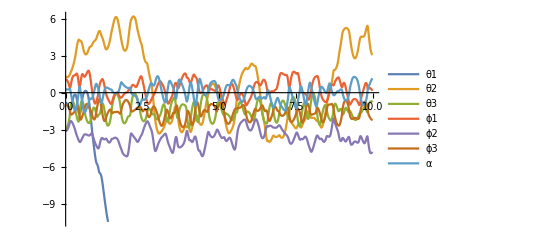

```mathematica
Plot[Evaluate[{θ1[t],θ2[t],θ3[t],ϕ1[t],ϕ2[t],ϕ3[t],α[t]}/. s1],{t,0,tf},PlotStyle->Automatic,PlotLegends->{θ1,θ2,θ3,ϕ1,ϕ2,ϕ3,α}]
```

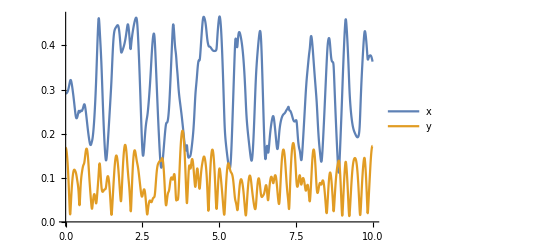

```mathematica
Plot[Evaluate[{x[t],y[t]}/. s1],{t,0,tf},PlotStyle->Automatic,PlotLegends->{x,y}]
```

```mathematica
timestep=0.01;
tf=10;
(*Create a list of the solution at different times with a step of'timestep' starting from 0 till the final simulation time*)

solList=Inner[Rule,Flatten[{q,dq,tim}],#,List]&/@Table[Flatten[{q,dq,t}/.s1[[1]]],{t,0,tf,timestep}];
```

```mathematica
(*Time axis for plot*)
time=tim/.solList;
```

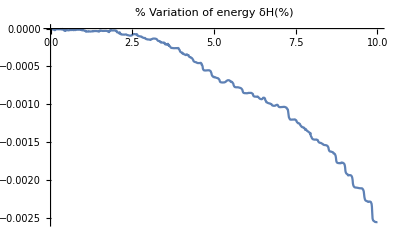

```mathematica
(*Energy Check*)
H=(tke+tpe)/.param/.solList;
δH=100*((H/H[[1]])-Table[1,{Length[solList]}]);
ListPlot[Inner[List,time,δH,List],Joined->True,PlotLabel->"% Variation of energy δH(%)"]
```

```mathematica
η
```

{a Cos[π/6+α[t]]+l Cos[θ1[t]]+r Cos[ϕ1[t]]-x[t],a Sin[π/6+α[t]]+l Sin[θ1[t]]+r Sin[ϕ1[t]]-y[t],b-a Cos[π/6-α[t]]+l Cos[θ2[t]]+r Cos[ϕ2[t]]-x[t],a Sin[π/6-α[t]]+l Sin[θ2[t]]+r Sin[ϕ2[t]]-y[t],b/2+l Cos[θ3[t]]+r Cos[ϕ3[t]]+a Sin[α[t]]-x[t],(√3 b)/2-a Cos[α[t]]+l Sin[θ3[t]]+r Sin[ϕ3[t]]-y[t]}

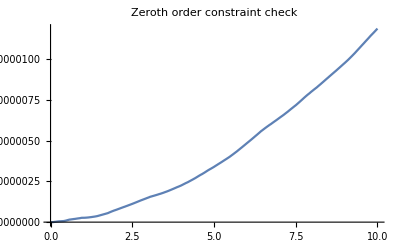

```mathematica
ηList=Table[Norm[(η)/.solList[[i]]/.param],{i,Length[solList]}];
ListPlot[Inner[List,time,ηList,List],Joined->True,PlotLabel->"Zeroth order constraint check"]
```

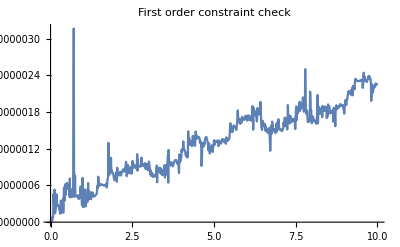

```mathematica
JηList=Table[Norm[Jηq.dq/.solList[[i]]/.param],{i,Length[solList]}];
ListPlot[Inner[List,time,JηList,List],Joined->True,PlotLabel->"First order constraint check"]
```

## Trajectory planning

```mathematica
figure[{l_,r_,a_,b_},param_]:=Module[{line1,line2,line3,circle1,circle2,circle3,circle4},
       line1=Graphics[{Black,Line[{{0,0},{b,0}}]}]/.param;
line2=Graphics[{Black,Line[{{b,0},{b/2,(Sqrt[3]*b)/2}}]}]/.param;
line3=Graphics[{Black,Line[{{b/2,(Sqrt[3]*b)/2},{0,0}}]}]/.param;
circle1=Graphics[{Red,Circle[{0,0},l+r+a]}]/.param;
circle2=Graphics[{Red,Circle[{b,0},l+r+a]}]/.param;
circle3=Graphics[{Red,Circle[{b/2,(Sqrt[3]*b)/2},l+r+a]}]/.param;
circle4=Graphics[{Blue,Circle[{b/2,b/(2 *Sqrt[3])},0.120 ]}]/.param;
Show[{line1,line2,line3,circle1,circle2,circle3,circle4}]
];
```

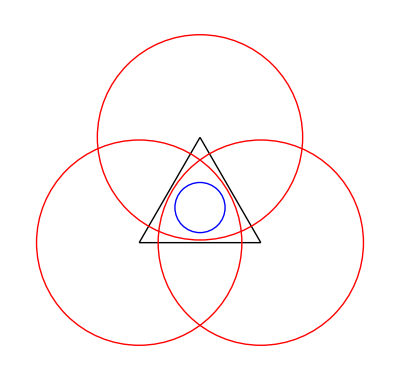

```mathematica
figure[{l,r,a,b},param]
```

```mathematica
(*Determining cubic trajectory coefficients*)
initconds={ϕ0->0,ϕf->2π,dϕ0->0,dϕf->0};
traj=a0+a1 t+a2 t^2+a3 t^3;
dtraj=D[traj,t];
eq1traj=(traj/.{t->0})-ϕ0;
eq2traj=(traj/.{t->tf})-ϕf;
eq3traj=(dtraj/.{t->0})-dϕ0;
eq4traj=(dtraj/.{t->tf})-dϕf;
solcoeff=Solve[{eq1traj,eq2traj,eq3traj,eq4traj}==0,{a0,a1,a2,a3}][[1]];
trajf=traj/.solcoeff/.initconds;
dtrajf=D[trajf,t];
```

```mathematica
(*Determining position velocity and acceleration on the circular trajectory*)
n=0.01;
(*pathparams={xc->b/2,yc->b/(2 *Sqrt[3]),a->120,b->120,tF->TF}/.param;
xpos=(xc+a Cos[ϕ])/.{ϕ->trajf}/.pathparams;
ypos=(yc+b Sin[ϕ])/.{ϕ->trajf}/.pathparams;
alphapos=0;
pos={xpos,ypos,alphapos};
pathvel=D[pos,t];
pathacc=D[pathvel,t];*)
pathparams={xc->b/2,yc->b/(2 *Sqrt[3]),rc->0.120,tfn->10}/.param;
xpos=(xc+rc Cos[ϕ])/.{ϕ->trajf}/.pathparams;
ypos=(yc+rc Sin[ϕ])/.{ϕ->trajf}/.pathparams;
αpos=0;
pos={xpos,ypos,αpos};
pathvel=D[pos,t];
pathacc=D[pathvel,t];
```

```mathematica
(*Discretizing position velocity and acceleration on the circular trajectory in task space for Inverse Dynamics*)

posv=Table[pos,{t,0,tf,n}];
velv=Table[pathvel,{t,0,tf,n}];
accv=Table[pathacc,{t,0,tf,n}];
```

## Inverse Dynamics

```mathematica
IK[{l_,r_,a_,b_,θ1_,θ2_,θ3_,ϕ1_,ϕ2_,ϕ3_,x_,y_,α_}]:=Module[{ik1,ik2,ik3,ik4,ik5,ik6,ik12,ik22,ik13,ik23,ik32,ik42,ik52,ik62,ik33,ik43,ik53,ik63,t,subs,subs2,subs3,solth1,solth2,solth3,angle111,angle112,angle121,angle122,angle211,angle212,angle221,angle222,ϕ1a,ϕ2a,ϕ3a,ϕ1b,ϕ2b,ϕ3b,branch1,branch2,branch3,branch4,branch5,branch6,branch7,branch8},

ik1= l Cos[θ1]+ r Cos[ϕ1]+ a Cos[(π/6)+ α]-x;
ik2= l Sin[θ1]+ r Sin[ϕ1]+ a Sin[(π/6)+ α]-y;
ik12=b+ l Cos[θ2]+ r Cos[ϕ2]+ a Cos[(5π/6)+ α]-x;
ik22= l Sin[θ2]+ r Sin[ϕ2]+ a Sin[(5π/6)+ α]-y;
ik13=b/2+ l Cos[θ3]+ r Cos[ϕ3]+ a Cos[(3π/2)+ α]-x;
ik23=Sqrt[3]b/2+ l Sin[θ3]+ r Sin[ϕ3]+ a Sin[(3π/2)+ α]-y;
ik3=Solve[{ik1,ik2}=={0,0},{Cos[ϕ1],Sin[ϕ1]}][[1]];
ik4=Simplify[Numerator[Together[(Cos[ϕ1]^2 + Sin[ϕ1]^2  -1)/.ik3]]];
Print[ik4];
subs={Cos[θ1]->(1-t^2)/(1+t^2),Sin[θ1]->(2 t /(1+t^2))};
ik5=Collect[Numerator[Together[TrigExpand[ik4]/.subs]],t];
ik6=Solve[ik5==0,t];
solth1={θ1->2*ArcTan[t/.ik6[[1]]],θ1->2*ArcTan[t/.ik6[[2]]]};
ik32=Solve[{ik12,ik22}=={0,0},{Cos[ϕ2],Sin[ϕ2]}][[1]];
ik42=Simplify[Numerator[Together[(Cos[ϕ2]^2 + Sin[ϕ2]^2  -1)/.ik32]]];
subs2={Cos[θ2]->(1-t^2)/(1+t^2),Sin[θ2]->(2 t /(1+t^2))};
ik52=Collect[Numerator[Together[TrigExpand[ik42]/.subs2]],t];
ik62=Simplify[Solve[ik52==0,t]];
solth2={θ2->2*ArcTan[t/.ik62[[1]]],θ2->2*ArcTan[t/.ik62[[2]]]};
ik33=Solve[{ik13,ik23}=={0,0},{Cos[ϕ3],Sin[ϕ3]}][[1]];
ik43=Numerator[Together[(Cos[ϕ3]^2 + Sin[ϕ3]^2  -1)/.ik33]];
subs3={Cos[θ3]->(1-t^2)/(1+t^2),Sin[θ3]->(2 t /(1+t^2))};
ik53=Collect[Numerator[Together[ik43/.subs3]],t];
ik63=Simplify[Solve[ik53==0,t]];
solth3={θ3->2*ArcTan[t/.ik63[[1]]],θ3->2*ArcTan[t/.ik63[[2]]]};
angle111={solth1[[1]],solth2[[1]],solth3[[1]]};
angle112={solth1[[1]],solth2[[1]],solth3[[2]]};
angle121={solth1[[1]],solth2[[2]],solth3[[1]]};
angle122={solth1[[1]],solth2[[2]],solth3[[2]]};
angle211={solth1[[2]],solth2[[1]],solth3[[1]]};
angle212={solth1[[2]],solth2[[1]],solth3[[2]]};
angle221={solth1[[2]],solth2[[2]],solth3[[1]]};
angle222={solth1[[2]],solth2[[2]],solth3[[2]]};
ϕ1a={ϕ1-> ArcTan[Cos[ϕ1]/.ik3,Sin[ϕ1]/.ik3]/.angle111};
ϕ1b= {ϕ1->ArcTan[Cos[ϕ1]/.ik3,Sin[ϕ1]/.ik3]/.angle211};
ϕ2a= {ϕ2->ArcTan[Cos[ϕ2]/.ik32,Sin[ϕ2]/.ik32]/.angle111};
ϕ2b= {ϕ2->ArcTan[Cos[ϕ2]/.ik32,Sin[ϕ2]/.ik32]/.angle222};
ϕ3a= {ϕ3->ArcTan[Cos[ϕ3]/.ik33,Sin[ϕ3]/.ik33]/.angle121};
ϕ3b= {ϕ3->ArcTan[Cos[ϕ3]/.ik33,Sin[ϕ3]/.ik33]/.angle222};branch1=Join[angle111,ϕ1a,ϕ2a,ϕ3a];
branch2=Join[angle112,ϕ1a,ϕ2a,ϕ3b];
branch3=Join[angle121,ϕ1a,ϕ2b,ϕ3a];
branch4=Join[angle122,ϕ1a,ϕ2b,ϕ3b];
branch5=Join[angle211,ϕ1b,ϕ2a,ϕ3a];
branch6=Join[angle212,ϕ1b,ϕ2a,ϕ3b];
branch7=Join[angle221,ϕ1b,ϕ2b,ϕ3a];
branch8=Join[angle222,ϕ1b,ϕ2b,ϕ3b];
Return[branch1];
]
```

```mathematica
solbr1=IK[{l,r,a,b,θ1,θ2,θ3,ϕ1,ϕ2,ϕ3,x,y,α}];
```

a^2+l^2-r^2+x^2+y^2-a (√3 x+y) Cos[α]+√3 a l Cos[α-θ1]-2 l x Cos[θ1]+a x Sin[α]-√3 a y Sin[α]-a l Sin[α-θ1]-2 l y Sin[θ1]

```mathematica
dθ1=D[((θ1/.solbr1)/.{x->x[t],y->y[t],α->α[t]}),t];
dθ2=D[((θ2/.solbr1)/.{x->x[t],y->y[t],α->α[t]}),t];
dθ3=D[((θ3/.solbr1)/.{x->x[t],y->y[t],α->α[t]}),t];
dϕ1=D[((ϕ1/.solbr1)/.{x->x[t],y->y[t],α->α[t]}),t];
dϕ2=D[((ϕ2/.solbr1)/.{x->x[t],y->y[t],α->α[t]}),t];
dϕ3=D[((ϕ3/.solbr1)/.{x->x[t],y->y[t],α->α[t]}),t];
```

```mathematica
ddθ1=D[dθ1,t];
ddθ2=D[dθ1,t];
ddθ3=D[dθ1,t];
ddϕ1=D[dϕ1,t];
ddϕ2=D[dϕ2,t];
ddϕ3=D[dϕ3,t];
```

```mathematica
jointposbranch1=Table[(solbr1/.param/.{x->posv[[ii]][[1]],y->posv[[ii]][[2]],α->posv[[ii]][[3]]}),{ii,1,Length[posv]}]
```

```mathematica
dθ1v=Table[(dθ1/.param/.{x[t]->posv[[ii]][[1]],y[t]->posv[[ii]][[2]],α[t]->posv[[ii]][[3]],x'[t]->velv[[ii]][[1]],y'[t]->velv[[ii]][[2]],α'[t]->velv[[ii]][[3]]}),{ii,1,Length[velv]}];
dθ2v=Table[(dθ2/.param/.{x[t]->posv[[ii]][[1]],y[t]->posv[[ii]][[2]],α[t]->posv[[ii]][[3]],x'[t]->velv[[ii]][[1]],y'[t]->velv[[ii]][[2]],α'[t]->velv[[ii]][[3]]}),{ii,1,Length[velv]}];
dθ3v=Table[(dθ3/.param/.{x[t]->posv[[ii]][[1]],y[t]->posv[[ii]][[2]],α[t]->posv[[ii]][[3]],x'[t]->velv[[ii]][[1]],y'[t]->velv[[ii]][[2]],α'[t]->velv[[ii]][[3]]}),{ii,1,Length[velv]}];
dϕ1v=Table[(dϕ1/.param/.{x[t]->posv[[ii]][[1]],y[t]->posv[[ii]][[2]],α[t]->posv[[ii]][[3]],x'[t]->velv[[ii]][[1]],y'[t]->velv[[ii]][[2]],α'[t]->velv[[ii]][[3]]}),{ii,1,Length[velv]}];
dϕ2v=Table[(dϕ2/.param/.{x[t]->posv[[ii]][[1]],y[t]->posv[[ii]][[2]],α[t]->posv[[ii]][[3]],x'[t]->velv[[ii]][[1]],y'[t]->velv[[ii]][[2]],α'[t]->velv[[ii]][[3]]}),{ii,1,Length[velv]}];
dϕ3v=Table[(dϕ3/.param/.{x[t]->posv[[ii]][[1]],y[t]->posv[[ii]][[2]],α[t]->posv[[ii]][[3]],x'[t]->velv[[ii]][[1]],y'[t]->velv[[ii]][[2]],α'[t]->velv[[ii]][[3]]}),{ii,1,Length[velv]}];
```

```mathematica
ddθ1v=Table[(ddθ1/.param/.{x[t]->posv[[ii]][[1]],y[t]->posv[[ii]][[2]],α[t]->posv[[ii]][[3]],x'[t]->velv[[ii]][[1]],y'[t]->velv[[ii]][[2]],α'[t]->velv[[ii]][[3]],x''[t]->accv[[ii]][[1]],y''[t]->accv[[ii]][[2]],α''[t]->accv[[ii]][[3]]}),{ii,1,Length[accv]}];
ddθ2v=Table[(ddθ2/.param/.{x[t]->posv[[ii]][[1]],y[t]->posv[[ii]][[2]],α[t]->posv[[ii]][[3]],x'[t]->velv[[ii]][[1]],y'[t]->velv[[ii]][[2]],α'[t]->velv[[ii]][[3]],x''[t]->accv[[ii]][[1]],y''[t]->accv[[ii]][[2]],α''[t]->accv[[ii]][[3]]}),{ii,1,Length[accv]}];
ddθ3v=Table[(ddθ3/.param/.{x[t]->posv[[ii]][[1]],y[t]->posv[[ii]][[2]],α[t]->posv[[ii]][[3]],x'[t]->velv[[ii]][[1]],y'[t]->velv[[ii]][[2]],α'[t]->velv[[ii]][[3]],x''[t]->accv[[ii]][[1]],y''[t]->accv[[ii]][[2]],α''[t]->accv[[ii]][[3]]}),{ii,1,Length[accv]}];
ddϕ1v=Table[(ddϕ1/.param/.{x[t]->posv[[ii]][[1]],y[t]->posv[[ii]][[2]],α[t]->posv[[ii]][[3]],x'[t]->velv[[ii]][[1]],y'[t]->velv[[ii]][[2]],α'[t]->velv[[ii]][[3]],x''[t]->accv[[ii]][[1]],y''[t]->accv[[ii]][[2]],α''[t]->accv[[ii]][[3]]}),{ii,1,Length[accv]}];
ddϕ2v=Table[(ddϕ2/.param/.{x[t]->posv[[ii]][[1]],y[t]->posv[[ii]][[2]],α[t]->posv[[ii]][[3]],x'[t]->velv[[ii]][[1]],y'[t]->velv[[ii]][[2]],α'[t]->velv[[ii]][[3]],x''[t]->accv[[ii]][[1]],y''[t]->accv[[ii]][[2]],α''[t]->accv[[ii]][[3]]}),{ii,1,Length[accv]}];
ddϕ3v=Table[(ddϕ3/.param/.{x[t]->posv[[ii]][[1]],y[t]->posv[[ii]][[2]],α[t]->posv[[ii]][[3]],x'[t]->velv[[ii]][[1]],y'[t]->velv[[ii]][[2]],α'[t]->velv[[ii]][[3]],x''[t]->accv[[ii]][[1]],y''[t]->accv[[ii]][[2]],α''[t]->accv[[ii]][[3]]}),{ii,1,Length[accv]}];
```

```mathematica
ddq1=D[dq,t]
```

{θ1''[t],θ2''[t],θ3''[t],ϕ1''[t],ϕ2''[t],ϕ3''[t],x''[t],y''[t],α''[t]}

```mathematica
tempinvdyn1=(M.ddq1+Transpose[Jηq].Inverse[A].(Jηdq.dq));
```

```mathematica
B=IdentityMatrix[9]-Transpose[Jηq].Inverse[A].Jηq.Inverse[M];
```

```mathematica
Jθ=D[η,{{θ1[t],θ2[t],θ3[t]}}]
Jϕ=D[η,{{ϕ1[t],ϕ2[t],ϕ3[t],x[t],y[t],α[t]}}]
```

{{-l Sin[θ1[t]],0,0},{l Cos[θ1[t]],0,0},{0,-l Sin[θ2[t]],0},{0,l Cos[θ2[t]],0},{0,0,-l Sin[θ3[t]]},{0,0,l Cos[θ3[t]]}}

{{-r Sin[ϕ1[t]],0,0,-1,0,-a Sin[π/6+α[t]]},{r Cos[ϕ1[t]],0,0,0,-1,a Cos[π/6+α[t]]},{0,-r Sin[ϕ2[t]],0,-1,0,-a Sin[π/6-α[t]]},{0,r Cos[ϕ2[t]],0,0,-1,-a Cos[π/6-α[t]]},{0,0,-r Sin[ϕ3[t]],-1,0,a Cos[α[t]]},{0,0,r Cos[ϕ3[t]],0,-1,a Sin[α[t]]}}

```mathematica
Jϕθ=Inverse[Jϕ].Jθ;
Jqθ=Join[IdentityMatrix[3],Jϕθ];
```

```mathematica
InvDyn[{q_,dq_,ddq_}]:=Module[{subsq,subsdq,subsddq, Av,Jηqv,Jηdqv,invdyntemp,B,Gv,Q,Jqθv,Qθ,Jϕθv},
subsq={θ1[t]->q[[1]],θ2[t]->q[[1]],θ3[t]->q[[1]],ϕ1[t]->q[[1]],ϕ2[t]->q[[1]],ϕ3[t]->q[[1]],x[t]->q[[1]],y[t]->q[[1]],α[t]->q[[1]]};
subsdq={θ1'[t]->dq[[1]],θ2'[t]->dq[[1]],θ3'[t]->dq[[1]],ϕ1'[t]->dq[[1]],ϕ2'[t]->dq[[1]],ϕ3'[t]->dq[[1]],x'[t]->dq[[1]],y'[t]->dq[[1]],α'[t]->dq[[1]]};
subsddq={θ1''[t]->ddq[[1]],θ2''[t]->ddq[[1]],θ3''[t]->ddq[[1]],ϕ1''[t]->ddq[[1]],ϕ2''[t]->ddq[[1]],ϕ3''[t]->ddq[[1]],x''[t]->ddq[[1]],y''[t]->ddq[[1]],α''[t]->ddq[[1]]};
Jηqv=Jηq/.param/.subsq;
(*Print[Jηqv];*)
Av=(Jηqv.Inverse[M].Transpose[Jηqv] )/.param/.subsq;
Print[Inverse[M]];
Print[Eigenvalues[Av]];
Print[Av];
(*Jηdqv=Jηq/.param/.subsq/.subsdq;
invdyntemp=M.ddq+Transpose[Jηqv].Inverse[Av].(Jηdqv.dq);
B=IdentityMatrix[9]-Transpose[Jηqv].Inverse[Av].Jηqv.Inverse[M];
Gv=G/.param/.subsq;
Jϕθv=Jϕθ/.param/.subsq/.subsdq;
Jqθv=Jqθ/.param/.subsq/.subsdq;
Q=PseudoInverse[B].invdyntemp+Gv;
Qθ=Transpose[Jqθv].Q;
Return[Qθ];*)
];
```

```mathematica
qv=Table[Join[({θ1,θ2,θ3,ϕ1,ϕ2,ϕ3}/.jointposbranch1[[ii]]),posv[[ii]]],{ii,1,Length[posv]}];
dqv=Table[Join[({dθ1v[[ii]],dθ2v[[ii]],dθ3v[[ii]],dϕ1v[[ii]],dϕ2v[[ii]],dϕ3v[[ii]]}),velv[[ii]]],{ii,1,Length[velv]}];
ddqv=Table[Join[({ddθ1v[[ii]],ddθ2v[[ii]],ddθ3v[[ii]],ddϕ1v[[ii]],ddϕ2v[[ii]],ddϕ3v[[ii]]}),accv[[ii]]],{ii,1,Length[accv]}];
```

```mathematica
Dimensions[Jsamp]
```

{6,9}

```mathematica
Dimensions[Msamp]
```

{9,9}

```mathematica
MatrixForm[Asamp]
```

(2.78604 | 3.59765 | 1.90155 | 0.450443 | 0.819142 | 0.174488
3.59765 | 18.9161 | -1.81038 | -0.326822 | 2.43531 | 0.755591
1.90155 | -1.81038 | 3.96378 | 5.52748 | -0.358597 | 0.50548
0.450443 | -0.326822 | 5.52748 | 17.7384 | -1.75534 | 1.93333
0.819142 | 2.43531 | -0.358597 | -1.75534 | 5.0462 | 3.54261
0.174488 | 0.755591 | 0.50548 | 1.93333 | 3.54261 | 16.656)

```mathematica
Inverse[Asamp]
```

{{-176781.,52593.5,182124.,-54326.6,-5342.28,1732.03},{52593.5,-13654.6,-52324.5,14644.3,-268.951,-988.908},{182124.,-52324.5,-178436.,52045.9,-3686.82,279.743},{-54326.6,14644.3,52045.9,-13224.1,2280.7,-1420.16},{-5342.28,-268.951,-3686.82,2280.7,9029.58,-2011.78},{1732.03,-988.908,279.743,-1420.16,-2011.78,2409.56}}

```mathematica
qv
```

```mathematica
Qv=ConstantArray[0,100];
```

```mathematica
For[ii=1,ii<=100,ii++,
Qv[[ii]]=InvDyn[{qv[[ii]],dqv[[ii]],ddqv[[ii]]}];
(*Print[Qv[[ii]]];*)
];
```

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,1.75015×10^-15}

{{2.78604,3.59765,1.90155,0.450443,0.819142,0.174488},{3.59765,18.9161,-1.81038,-0.326822,2.43531,0.755591},{1.90155,-1.81038,3.96378,5.52748,-0.358597,0.50548},{0.450443,-0.326822,5.52748,17.7384,-1.75534,1.93333},{0.819142,2.43531,-0.358597,-1.75534,5.0462,3.54261},{0.174488,0.755591,0.50548,1.93333,3.54261,16.656}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,-4.57412×10^-16}

{{2.78596,3.59746,1.90157,0.450469,0.819111,0.174489},{3.59746,18.9162,-1.81035,-0.326838,2.43531,0.755622},{1.90157,-1.81035,3.96365,5.52732,-0.358582,0.505453},{0.450469,-0.326838,5.52732,17.7385,-1.75537,1.93332},{0.819111,2.43531,-0.358582,-1.75537,5.04611,3.54248},{0.174489,0.755622,0.505453,1.93332,3.54248,16.6561}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,6.46147×10^-16}

{{2.78571,3.59689,1.90162,0.450548,0.819019,0.174491},{3.59689,18.9165,-1.81027,-0.326886,2.43531,0.755714},{1.90162,-1.81027,3.96326,5.52683,-0.358538,0.505372},{0.450548,-0.326886,5.52683,17.7389,-1.75545,1.93327},{0.819019,2.43531,-0.358538,-1.75545,5.04586,3.54207},{0.174491,0.755714,0.505372,1.93327,3.54207,16.6563}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,6.31041×10^-16}

{{2.78528,3.59594,1.9017,0.450679,0.818866,0.174495},{3.59594,18.9169,-1.81014,-0.326966,2.43532,0.755867},{1.9017,-1.81014,3.96261,5.52602,-0.358465,0.505237},{0.450679,-0.326966,5.52602,17.7396,-1.75558,1.9332},{0.818866,2.43532,-0.358465,-1.75558,5.04545,3.54139},{0.174495,0.755867,0.505237,1.9332,3.54139,16.6567}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,-2.14844×10^-16}

{{2.78469,3.59462,1.90181,0.450862,0.818651,0.1745},{3.59462,18.9175,-1.80996,-0.327077,2.43532,0.756081},{1.90181,-1.80996,3.96171,5.52489,-0.358362,0.505049},{0.450862,-0.327077,5.52489,17.7405,-1.75577,1.93309},{0.818651,2.43532,-0.358362,-1.75577,5.04486,3.54043},{0.1745,0.756081,0.505049,1.93309,3.54043,16.6573}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,-1.69648×10^-16}

{{2.78393,3.59292,1.90195,0.451097,0.818376,0.174507},{3.59292,18.9182,-1.80972,-0.327221,2.43533,0.756357},{1.90195,-1.80972,3.96054,5.52344,-0.35823,0.504807},{0.451097,-0.327221,5.52344,17.7416,-1.75601,1.93296},{0.818376,2.43533,-0.35823,-1.75601,5.04412,3.53921},{0.174507,0.756357,0.504807,1.93296,3.53921,16.6581}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,2.25375×10^-16}

{{2.78301,3.59084,1.90213,0.451384,0.818039,0.174515},{3.59084,18.9192,-1.80944,-0.327396,2.43534,0.756693},{1.90213,-1.80944,3.95912,5.52166,-0.358069,0.504512},{0.451384,-0.327396,5.52166,17.7431,-1.75631,1.9328},{0.818039,2.43534,-0.358069,-1.75631,5.04321,3.53771},{0.174515,0.756693,0.504512,1.9328,3.53771,16.659}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,2.05847×10^-16}

{{2.78192,3.58838,1.90233,0.451723,0.817643,0.174524},{3.58838,18.9203,-1.8091,-0.327602,2.43535,0.75709},{1.90233,-1.8091,3.95744,5.51957,-0.357878,0.504163},{0.451723,-0.327602,5.51957,17.7447,-1.75666,1.93261},{0.817643,2.43535,-0.357878,-1.75666,5.04213,3.53594},{0.174524,0.75709,0.504163,1.93261,3.53594,16.66}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,4.95375×10^-16}

{{2.78066,3.58555,1.90257,0.452114,0.817185,0.174535},{3.58555,18.9215,-1.80871,-0.32784,2.43536,0.757547},{1.90257,-1.80871,3.9555,5.51715,-0.357659,0.503762},{0.452114,-0.32784,5.51715,17.7467,-1.75706,1.93239},{0.817185,2.43536,-0.357659,-1.75706,5.04089,3.53391},{0.174535,0.757547,0.503762,1.93239,3.53391,16.6613}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,1.3248×10^-15}

{{2.77924,3.58235,1.90284,0.452557,0.816667,0.174546},{3.58235,18.9229,-1.80826,-0.328109,2.43537,0.758065},{1.90284,-1.80826,3.95331,5.51441,-0.35741,0.503308},{0.452557,-0.328109,5.51441,17.7489,-1.75751,1.93214},{0.816667,2.43537,-0.35741,-1.75751,5.03949,3.5316},{0.174546,0.758065,0.503308,1.93214,3.5316,16.6627}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,3.90749×10^-16}

{{2.77765,3.57878,1.90314,0.453051,0.816089,0.174559},{3.57878,18.9245,-1.80777,-0.328409,2.43538,0.758643},{1.90314,-1.80777,3.95087,5.51136,-0.357132,0.502801},{0.453051,-0.328409,5.51136,17.7513,-1.75802,1.93186},{0.816089,2.43538,-0.357132,-1.75802,5.03792,3.52903},{0.174559,0.758643,0.502801,1.93186,3.52903,16.6642}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,1.87508×10^-16}

{{2.7759,3.57483,1.90347,0.453597,0.815451,0.174573},{3.57483,18.9263,-1.80722,-0.32874,2.43539,0.759281},{1.90347,-1.80722,3.94818,5.50798,-0.356825,0.502241},{0.453597,-0.32874,5.50798,17.754,-1.75858,1.93156},{0.815451,2.43539,-0.356825,-1.75858,5.0362,3.52618},{0.174573,0.759281,0.502241,1.93156,3.52618,16.666}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,-8.36313×10^-16}

{{2.77399,3.57051,1.90383,0.454194,0.814753,0.174588},{3.57051,18.9282,-1.80663,-0.329102,2.43541,0.759979},{1.90383,-1.80663,3.94523,5.50429,-0.356489,0.501629},{0.454194,-0.329102,5.50429,17.7569,-1.75919,1.93122},{0.814753,2.43541,-0.356489,-1.75919,5.03431,3.52307},{0.174588,0.759979,0.501629,1.93122,3.52307,16.6679}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,-3.81829×10^-17}

{{2.77192,3.56582,1.90423,0.454842,0.813995,0.174603},{3.56582,18.9303,-1.80598,-0.329495,2.43542,0.760737},{1.90423,-1.80598,3.94204,5.50028,-0.356124,0.500965},{0.454842,-0.329495,5.50028,17.7601,-1.75986,1.93086},{0.813995,2.43542,-0.356124,-1.75986,5.03227,3.51969},{0.174603,0.760737,0.500965,1.93086,3.51969,16.6699}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,-4.68337×10^-16}

{{2.76969,3.56076,1.90465,0.455542,0.813178,0.17462},{3.56076,18.9325,-1.80528,-0.329918,2.43544,0.761555},{1.90465,-1.80528,3.93859,5.49595,-0.355729,0.500249},{0.455542,-0.329918,5.49595,17.7636,-1.76057,1.93046},{0.813178,2.43544,-0.355729,-1.76057,5.03007,3.51605},{0.17462,0.761555,0.500249,1.93046,3.51605,16.6721}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,-3.71431×10^-18}

{{2.7673,3.55533,1.9051,0.456292,0.812301,0.174637},{3.55533,18.9349,-1.80453,-0.330371,2.43546,0.762431},{1.9051,-1.80453,3.9349,5.4913,-0.355306,0.499481},{0.456292,-0.330371,5.4913,17.7673,-1.76134,1.93004},{0.812301,2.43546,-0.355306,-1.76134,5.02771,3.51214},{0.174637,0.762431,0.499481,1.93004,3.51214,16.6745}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,4.82523×10^-16}

{{2.76475,3.54953,1.90559,0.457094,0.811366,0.174655},{3.54953,18.9374,-1.80373,-0.330854,2.43548,0.763367},{1.90559,-1.80373,3.93097,5.48634,-0.354853,0.498662},{0.457094,-0.330854,5.48634,17.7712,-1.76216,1.92959},{0.811366,2.43548,-0.354853,-1.76216,5.02519,3.50796},{0.174655,0.763367,0.498662,1.92959,3.50796,16.677}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,-4.07635×10^-16}

{{2.76205,3.54336,1.9061,0.457947,0.810371,0.174672},{3.54336,18.9401,-1.80287,-0.331367,2.43549,0.764362},{1.9061,-1.80287,3.92679,5.48107,-0.354371,0.497792},{0.457947,-0.331367,5.48107,17.7754,-1.76303,1.9291},{0.810371,2.43549,-0.354371,-1.76303,5.02252,3.50352},{0.174672,0.764362,0.497792,1.9291,3.50352,16.6797}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,-9.04629×10^-16}

{{2.75919,3.53683,1.90664,0.45885,0.809317,0.174691},{3.53683,18.943,-1.80197,-0.331909,2.43551,0.765416},{1.90664,-1.80197,3.92237,5.47547,-0.35386,0.49687},{0.45885,-0.331909,5.47547,17.7798,-1.76395,1.92859},{0.809317,2.43551,-0.35386,-1.76395,5.01969,3.49881},{0.174691,0.765416,0.49687,1.92859,3.49881,16.6825}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,-3.21389×10^-18}

{{2.75618,3.52993,1.90721,0.459804,0.808205,0.174709},{3.52993,18.946,-1.80102,-0.332481,2.43553,0.766528},{1.90721,-1.80102,3.9177,5.46957,-0.35332,0.495898},{0.459804,-0.332481,5.46957,17.7845,-1.76492,1.92805},{0.808205,2.43553,-0.35332,-1.76492,5.01671,3.49384},{0.174709,0.766528,0.495898,1.92805,3.49384,16.6855}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,4.1624×10^-16}

{{2.75301,3.52267,1.90781,0.460809,0.807034,0.174727},{3.52267,18.9492,-1.80001,-0.333082,2.43555,0.767699},{1.90781,-1.80001,3.9128,5.46335,-0.35275,0.494875},{0.460809,-0.333082,5.46335,17.7894,-1.76595,1.92748},{0.807034,2.43555,-0.35275,-1.76595,5.01358,3.48861},{0.174727,0.767699,0.494875,1.92748,3.48861,16.6886}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,9.23826×10^-16}

{{2.7497,3.51504,1.90844,0.461864,0.805805,0.174745},{3.51504,18.9525,-1.79896,-0.333712,2.43557,0.768928},{1.90844,-1.79896,3.90766,5.45681,-0.352151,0.493801},{0.461864,-0.333712,5.45681,17.7945,-1.76702,1.92688},{0.805805,2.43557,-0.352151,-1.76702,5.0103,3.48311},{0.174745,0.768928,0.493801,1.92688,3.48311,16.6919}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,1.31157×10^-15}

{{2.74624,3.50705,1.9091,0.46297,0.804518,0.174762},{3.50705,18.9559,-1.79785,-0.334371,2.43558,0.770215},{1.9091,-1.79785,3.90228,5.44996,-0.351523,0.492678},{0.46297,-0.334371,5.44996,17.7999,-1.76814,1.92626},{0.804518,2.43558,-0.351523,-1.76814,5.00686,3.47735},{0.174762,0.770215,0.492678,1.92626,3.47735,16.6953}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,-4.40926×10^-16}

{{2.74263,3.4987,1.90979,0.464126,0.803173,0.174779},{3.4987,18.9595,-1.7967,-0.335058,2.4356,0.771559},{1.90979,-1.7967,3.89667,5.4428,-0.350865,0.491505},{0.464126,-0.335058,5.4428,17.8055,-1.76932,1.9256},{0.803173,2.4356,-0.350865,-1.76932,5.00328,3.47132},{0.174779,0.771559,0.491505,1.9256,3.47132,16.6989}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,6.84722×10^-16}

{{2.73887,3.48999,1.91051,0.465333,0.801771,0.174796},{3.48999,18.9633,-1.79549,-0.335773,2.43562,0.772962},{1.91051,-1.79549,3.89082,5.43532,-0.350178,0.490282},{0.465333,-0.335773,5.43532,17.8113,-1.77054,1.92491},{0.801771,2.43562,-0.350178,-1.77054,4.99956,3.46504},{0.174796,0.772962,0.490282,1.92491,3.46504,16.7026}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,6.75081×10^-16}

{{2.73498,3.48091,1.91125,0.466589,0.800311,0.174811},{3.48091,18.9672,-1.79423,-0.336516,2.43563,0.774421},{1.91125,-1.79423,3.88475,5.42754,-0.349461,0.489011},{0.466589,-0.336516,5.42754,17.8174,-1.77181,1.92419},{0.800311,2.43563,-0.349461,-1.77181,4.99569,3.45849},{0.174811,0.774421,0.489011,1.92419,3.45849,16.7065}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,-1.9199×10^-16}

{{2.73094,3.47148,1.91202,0.467896,0.798794,0.174825},{3.47148,18.9712,-1.79293,-0.337287,2.43565,0.775938},{1.91202,-1.79293,3.87845,5.41944,-0.348715,0.48769},{0.467896,-0.337287,5.41944,17.8237,-1.77313,1.92345},{0.798794,2.43565,-0.348715,-1.77313,4.99167,3.45169},{0.174825,0.775938,0.48769,1.92345,3.45169,16.7105}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,6.70809×10^-16}

{{2.72676,3.46169,1.91282,0.469252,0.797221,0.174838},{3.46169,18.9754,-1.79157,-0.338085,2.43566,0.777512},{1.91282,-1.79157,3.87192,5.41102,-0.347939,0.48632},{0.469252,-0.338085,5.41102,17.8303,-1.7745,1.92267},{0.797221,2.43566,-0.347939,-1.7745,4.98751,3.44462},{0.174838,0.777512,0.48632,1.92267,3.44462,16.7147}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,-2.6861×10^-16}

{{2.72244,3.45153,1.91364,0.470659,0.79559,0.174849},{3.45153,18.9797,-1.79016,-0.33891,2.43567,0.779142},{1.91364,-1.79016,3.86516,5.4023,-0.347134,0.484903},{0.470659,-0.33891,5.4023,17.837,-1.77592,1.92187},{0.79559,2.43567,-0.347134,-1.77592,4.98322,3.43729},{0.174849,0.779142,0.484903,1.92187,3.43729,16.719}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,-4.61714×10^-17}

{{2.71799,3.44103,1.91449,0.472115,0.793903,0.174859},{3.44103,18.9842,-1.78871,-0.339762,2.43568,0.780829},{1.91449,-1.78871,3.85819,5.39327,-0.346299,0.483437},{0.472115,-0.339762,5.39327,17.844,-1.77738,1.92103},{0.793903,2.43568,-0.346299,-1.77738,4.97878,3.4297},{0.174859,0.780829,0.483437,1.92103,3.4297,16.7234}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,6.42324×10^-16}

{{2.7134,3.43016,1.91537,0.473621,0.79216,0.174866},{3.43016,18.9888,-1.7872,-0.34064,2.43569,0.782572},{1.91537,-1.7872,3.85099,5.38393,-0.345434,0.481924},{0.473621,-0.34064,5.38393,17.8512,-1.7789,1.92017},{0.79216,2.43569,-0.345434,-1.7789,4.9742,3.42186},{0.174866,0.782572,0.481924,1.92017,3.42186,16.728}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,-2.07519×10^-16}

{{2.70868,3.41894,1.91628,0.475176,0.790361,0.174872},{3.41894,18.9935,-1.78565,-0.341544,2.43569,0.784371},{1.91628,-1.78565,3.84358,5.37427,-0.344539,0.480363},{0.475176,-0.341544,5.37427,17.8586,-1.78046,1.91927},{0.790361,2.43569,-0.344539,-1.78046,4.96949,3.41376},{0.174872,0.784371,0.480363,1.91927,3.41376,16.7327}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,-4.53056×10^-17}

{{2.70383,3.40737,1.91721,0.476781,0.788506,0.174875},{3.40737,18.9983,-1.78404,-0.342474,2.4357,0.786226},{1.91721,-1.78404,3.83595,5.36431,-0.343614,0.478755},{0.476781,-0.342474,5.36431,17.8662,-1.78207,1.91835},{0.788506,2.4357,-0.343614,-1.78207,4.96465,3.40539},{0.174875,0.786226,0.478755,1.91835,3.40539,16.7375}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,6.71643×10^-16}

{{2.69885,3.39544,1.91816,0.478435,0.786596,0.174875},{3.39544,19.0033,-1.78239,-0.343429,2.4357,0.788136},{1.91816,-1.78239,3.8281,5.35404,-0.342659,0.477101},{0.478435,-0.343429,5.35404,17.8741,-1.78372,1.91739},{0.786596,2.4357,-0.342659,-1.78372,4.95967,3.39678},{0.174875,0.788136,0.477101,1.91739,3.39678,16.7425}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,-2.1971×10^-16}

{{2.69375,3.38316,1.91914,0.480138,0.784631,0.174872},{3.38316,19.0084,-1.78068,-0.34441,2.43569,0.790102},{1.91914,-1.78068,3.82005,5.34346,-0.341674,0.4754},{0.480138,-0.34441,5.34346,17.8821,-1.78542,1.91641},{0.784631,2.43569,-0.341674,-1.78542,4.95456,3.3879},{0.174872,0.790102,0.4754,1.91641,3.3879,16.7476}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,-1.93821×10^-16}

{{2.68852,3.37053,1.92015,0.481891,0.78261,0.174866},{3.37053,19.0137,-1.77893,-0.345415,2.43569,0.792122},{1.92015,-1.77893,3.81179,5.33257,-0.340659,0.473653},{0.481891,-0.345415,5.33257,17.8904,-1.78717,1.91539},{0.78261,2.43569,-0.340659,-1.78717,4.94933,3.37877},{0.174866,0.792122,0.473653,1.91539,3.37877,16.7528}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,1.09778×10^-15}

{{2.68317,3.35755,1.92118,0.483692,0.780535,0.174857},{3.35755,19.019,-1.77713,-0.346444,2.43568,0.794197},{1.92118,-1.77713,3.80332,5.32137,-0.339613,0.471861},{0.483692,-0.346444,5.32137,17.8989,-1.78896,1.91435},{0.780535,2.43568,-0.339613,-1.78896,4.94396,3.36938},{0.174857,0.794197,0.471861,1.91435,3.36938,16.7582}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,-1.90832×10^-16}

{{2.6777,3.34422,1.92223,0.485543,0.778406,0.174844},{3.34422,19.0245,-1.77528,-0.347498,2.43567,0.796327},{1.92223,-1.77528,3.79465,5.30987,-0.338538,0.470023},{0.485543,-0.347498,5.30987,17.9075,-1.7908,1.91327},{0.778406,2.43567,-0.338538,-1.7908,4.93847,3.35974},{0.174844,0.796327,0.470023,1.91327,3.35974,16.7637}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,8.44493×10^-16}

{{2.67212,3.33055,1.92331,0.487442,0.776223,0.174828},{3.33055,19.03,-1.77338,-0.348575,2.43565,0.79851},{1.92331,-1.77338,3.78578,5.29805,-0.337431,0.468141},{0.487442,-0.348575,5.29805,17.9164,-1.79268,1.91216},{0.776223,2.43565,-0.337431,-1.79268,4.93286,3.34985},{0.174828,0.79851,0.468141,1.91216,3.34985,16.7693}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,9.01247×10^-16}

{{2.66643,3.31652,1.92441,0.48939,0.773985,0.174807},{3.31652,19.0357,-1.77143,-0.349676,2.43563,0.800747},{1.92441,-1.77143,3.7767,5.28594,-0.336295,0.466214},{0.48939,-0.349676,5.28594,17.9255,-1.79461,1.91103},{0.773985,2.43563,-0.336295,-1.79461,4.92713,3.3397},{0.174807,0.800747,0.466214,1.91103,3.3397,16.775}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,4.19517×10^-16}

{{2.66062,3.30215,1.92553,0.491387,0.771694,0.174781},{3.30215,19.0416,-1.76943,-0.350799,2.4356,0.803038},{1.92553,-1.76943,3.76744,5.27351,-0.335127,0.464243},{0.491387,-0.350799,5.27351,17.9347,-1.79658,1.90986},{0.771694,2.4356,-0.335127,-1.79658,4.92128,3.3293},{0.174781,0.803038,0.464243,1.90986,3.3293,16.7809}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,-2.09982×10^-16}

{{2.6547,3.28744,1.92668,0.493432,0.76935,0.174751},{3.28744,19.0475,-1.76739,-0.351945,2.43557,0.805382},{1.92668,-1.76739,3.75798,5.26078,-0.333929,0.462228},{0.493432,-0.351945,5.26078,17.9442,-1.79859,1.90866},{0.76935,2.43557,-0.333929,-1.79859,4.91531,3.31864},{0.174751,0.805382,0.462228,1.90866,3.31864,16.7869}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,4.18238×10^-16}

{{2.64868,3.27238,1.92785,0.495526,0.766953,0.174716},{3.27238,19.0535,-1.7653,-0.353113,2.43554,0.807779},{1.92785,-1.7653,3.74833,5.24775,-0.3327,0.460169},{0.495526,-0.353113,5.24775,17.9538,-1.80065,1.90743},{0.766953,2.43554,-0.3327,-1.80065,4.90922,3.30773},{0.174716,0.807779,0.460169,1.90743,3.30773,16.793}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,-4.35404×10^-16}

{{2.64255,3.25698,1.92903,0.497667,0.764504,0.174675},{3.25698,19.0596,-1.76315,-0.354302,2.4355,0.810229},{1.92903,-1.76315,3.73849,5.2344,-0.33144,0.458068},{0.497667,-0.354302,5.2344,17.9637,-1.80275,1.90617},{0.764504,2.4355,-0.33144,-1.80275,4.90302,3.29658},{0.174675,0.810229,0.458068,1.90617,3.29658,16.7991}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,-6.35967×10^-16}

{{2.63632,3.24123,1.93025,0.499857,0.762002,0.174629},{3.24123,19.0659,-1.76096,-0.355513,2.43545,0.812731},{1.93025,-1.76096,3.72847,5.22076,-0.330149,0.455925},{0.499857,-0.355513,5.22076,17.9737,-1.8049,1.90488},{0.762002,2.43545,-0.330149,-1.8049,4.89671,3.28517},{0.174629,0.812731,0.455925,1.90488,3.28517,16.8055}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,-1.72226×10^-16}

{{2.62999,3.22515,1.93148,0.502095,0.759448,0.174577},{3.22515,19.0722,-1.75873,-0.356745,2.4354,0.815285},{1.93148,-1.75873,3.71827,5.20681,-0.328827,0.453739},{0.502095,-0.356745,5.20681,17.9839,-1.80708,1.90356},{0.759448,2.4354,-0.328827,-1.80708,4.8903,3.27351},{0.174577,0.815285,0.453739,1.90356,3.27351,16.8119}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,2.15322×10^-16}

{{2.62357,3.20873,1.93273,0.504381,0.756842,0.174518},{3.20873,19.0786,-1.75644,-0.357997,2.43534,0.81789},{1.93273,-1.75644,3.70788,5.19256,-0.327473,0.451512},{0.504381,-0.357997,5.19256,17.9943,-1.80931,1.90221},{0.756842,2.43534,-0.327473,-1.80931,4.88377,3.2616},{0.174518,0.81789,0.451512,1.90221,3.2616,16.8184}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,-4.81795×10^-16}

{{2.61705,3.19197,1.934,0.506714,0.754185,0.174453},{3.19197,19.0851,-1.75411,-0.35927,2.43527,0.820547},{1.934,-1.75411,3.69733,5.178,-0.326089,0.449243},{0.506714,-0.35927,5.178,18.0048,-1.81158,1.90082},{0.754185,2.43527,-0.326089,-1.81158,4.87714,3.24944},{0.174453,0.820547,0.449243,1.90082,3.24944,16.825}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,9.10471×10^-16}

{{2.61045,3.17487,1.93529,0.509095,0.751477,0.174382},{3.17487,19.0917,-1.75173,-0.360562,2.4352,0.823255},{1.93529,-1.75173,3.6866,5.16314,-0.324673,0.446934},{0.509095,-0.360562,5.16314,18.0156,-1.81389,1.89941},{0.751477,2.4352,-0.324673,-1.81389,4.87041,3.23704},{0.174382,0.823255,0.446934,1.89941,3.23704,16.8318}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,2.72488×10^-16}

{{2.60375,3.15744,1.93661,0.511524,0.748719,0.174303},{3.15744,19.0984,-1.7493,-0.361873,2.43512,0.826014},{1.93661,-1.7493,3.67569,5.14798,-0.323225,0.444584},{0.511524,-0.361873,5.14798,18.0265,-1.81624,1.89796},{0.748719,2.43512,-0.323225,-1.81624,4.86358,3.22438},{0.174303,0.826014,0.444584,1.89796,3.22438,16.8386}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,4.99499×10^-16}

{{2.59697,3.13968,1.93794,0.514,0.74591,0.174217},{3.13968,19.1052,-1.74682,-0.363203,2.43504,0.828823},{1.93794,-1.74682,3.66463,5.13252,-0.321746,0.442194},{0.514,-0.363203,5.13252,18.0375,-1.81863,1.89648},{0.74591,2.43504,-0.321746,-1.81863,4.85665,3.21149},{0.174217,0.828823,0.442194,1.89648,3.21149,16.8455}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,-2.82494×10^-17}

{{2.59011,3.12158,1.93928,0.516523,0.743051,0.174123},{3.12158,19.1121,-1.7443,-0.364551,2.43494,0.831682},{1.93928,-1.7443,3.6534,5.11676,-0.320235,0.439765},{0.516523,-0.364551,5.11676,18.0488,-1.82106,1.89497},{0.743051,2.43494,-0.320235,-1.82106,4.84963,3.19834},{0.174123,0.831682,0.439765,1.89497,3.19834,16.8525}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,3.94016×10^-16}

{{2.58317,3.10316,1.94065,0.519093,0.740142,0.174021},{3.10316,19.119,-1.74173,-0.365917,2.43484,0.834591},{1.94065,-1.74173,3.64201,5.1007,-0.318692,0.437298},{0.519093,-0.365917,5.1007,18.0602,-1.82352,1.89342},{0.740142,2.43484,-0.318692,-1.82352,4.84251,3.18495},{0.174021,0.834591,0.437298,1.89342,3.18495,16.8597}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,6.7971×10^-16}

{{2.57616,3.0844,1.94203,0.521709,0.737184,0.17391},{3.0844,19.126,-1.73911,-0.3673,2.43473,0.837549},{1.94203,-1.73911,3.63046,5.08434,-0.317118,0.434791},{0.521709,-0.3673,5.08434,18.0717,-1.82603,1.89185},{0.737184,2.43473,-0.317118,-1.82603,4.83531,3.17132},{0.17391,0.837549,0.434791,1.89185,3.17132,16.8669}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,3.37998×10^-16}

{{2.56907,3.06531,1.94343,0.524373,0.734177,0.173791},{3.06531,19.1331,-1.73645,-0.3687,2.43461,0.840555},{1.94343,-1.73645,3.61875,5.06768,-0.315511,0.432247},{0.524373,-0.3687,5.06768,18.0834,-1.82857,1.89024},{0.734177,2.43461,-0.315511,-1.82857,4.82801,3.15744},{0.173791,0.840555,0.432247,1.89024,3.15744,16.8742}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,1.57415×10^-17}

{{2.56191,3.0459,1.94485,0.527083,0.731122,0.173663},{3.0459,19.1403,-1.73374,-0.370117,2.43448,0.843611},{1.94485,-1.73374,3.6069,5.05072,-0.313872,0.429665},{0.527083,-0.370117,5.05072,18.0953,-1.83116,1.8886},{0.731122,2.43448,-0.313872,-1.83116,4.82063,3.14332},{0.173663,0.843611,0.429665,1.8886,3.14332,16.8815}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,-6.79136×10^-16}

{{2.55468,3.02616,1.94628,0.52984,0.728018,0.173525},{3.02616,19.1475,-1.73098,-0.371549,2.43435,0.846714},{1.94628,-1.73098,3.5949,5.03347,-0.312201,0.427046},{0.52984,-0.371549,5.03347,18.1073,-1.83378,1.88693},{0.728018,2.43435,-0.312201,-1.83378,4.81317,3.12896},{0.173525,0.846714,0.427046,1.88693,3.12896,16.889}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,-6.51206×10^-16}

{{2.54739,3.0061,1.94773,0.532643,0.724867,0.173378},{3.0061,19.1548,-1.72818,-0.372998,2.4342,0.849866},{1.94773,-1.72818,3.58276,5.01591,-0.310498,0.42439},{0.532643,-0.372998,5.01591,18.1194,-1.83643,1.88523},{0.724867,2.4342,-0.310498,-1.83643,4.80562,3.11436},{0.173378,0.849866,0.42439,1.88523,3.11436,16.8966}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,3.33321×10^-16}

{{2.54004,2.98572,1.94919,0.535491,0.721668,0.173221},{2.98572,19.1621,-1.72533,-0.374461,2.43404,0.853065},{1.94919,-1.72533,3.57047,4.99806,-0.308763,0.421699},{0.535491,-0.374461,4.99806,18.1317,-1.83912,1.8835},{0.721668,2.43404,-0.308763,-1.83912,4.798,3.09951},{0.173221,0.853065,0.421699,1.8835,3.09951,16.9042}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,-7.63829×10^-16}

{{2.53263,2.96502,1.95067,0.538386,0.718422,0.173053},{2.96502,19.1695,-1.72244,-0.375938,2.43387,0.85631},{1.95067,-1.72244,3.55805,4.97992,-0.306995,0.418972},{0.538386,-0.375938,4.97992,18.1441,-1.84185,1.88173},{0.718422,2.43387,-0.306995,-1.84185,4.7903,3.08443},{0.173053,0.85631,0.418972,1.88173,3.08443,16.9119}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,-1.05239×10^-16}

{{2.52517,2.944,1.95216,0.541326,0.71513,0.172875},{2.944,19.177,-1.7195,-0.37743,2.4337,0.859603},{1.95216,-1.7195,3.54549,4.96148,-0.305194,0.41621},{0.541326,-0.37743,4.96148,18.1567,-1.84461,1.87993},{0.71513,2.4337,-0.305194,-1.84461,4.78253,3.06911},{0.172875,0.859603,0.41621,1.87993,3.06911,16.9196}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,2.32796×10^-16}

{{2.51766,2.92266,1.95367,0.544312,0.711792,0.172685},{2.92266,19.1845,-1.71651,-0.378935,2.43351,0.862941},{1.95367,-1.71651,3.53281,4.94275,-0.303361,0.413413},{0.544312,-0.378935,4.94275,18.1694,-1.84741,1.87809},{0.711792,2.43351,-0.303361,-1.84741,4.77468,3.05356},{0.172685,0.862941,0.413413,1.87809,3.05356,16.9275}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,-3.07626×10^-18}

{{2.51009,2.901,1.95519,0.547344,0.708407,0.172485},{2.901,19.1921,-1.71348,-0.380454,2.43331,0.866325},{1.95519,-1.71348,3.51999,4.92373,-0.301495,0.410582},{0.547344,-0.380454,4.92373,18.1822,-1.85024,1.87623},{0.708407,2.43331,-0.301495,-1.85024,4.76677,3.03776},{0.172485,0.866325,0.410582,1.87623,3.03776,16.9354}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,2.41238×10^-16}

{{2.50248,2.87904,1.95672,0.55042,0.704978,0.172272},{2.87904,19.1997,-1.7104,-0.381985,2.43309,0.869755},{1.95672,-1.7104,3.50706,4.90441,-0.299596,0.407718},{0.55042,-0.381985,4.90441,18.1951,-1.8531,1.87433},{0.704978,2.43309,-0.299596,-1.8531,4.7588,3.02174},{0.172272,0.869755,0.407718,1.87433,3.02174,16.9434}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,9.38136×10^-17}

{{2.49483,2.85676,1.95826,0.553541,0.701503,0.172048},{2.85676,19.2073,-1.70728,-0.383528,2.43287,0.873229},{1.95826,-1.70728,3.494,4.8848,-0.297664,0.404822},{0.553541,-0.383528,4.8848,18.2082,-1.856,1.8724},{0.701503,2.43287,-0.297664,-1.856,4.75076,3.00548},{0.172048,0.873229,0.404822,1.8724,3.00548,16.9514}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,-9.04183×10^-16}

{{2.48715,2.83417,1.95981,0.556707,0.697984,0.171811},{2.83417,19.215,-1.70411,-0.385082,2.43263,0.876748},{1.95981,-1.70411,3.48083,4.86491,-0.2957,0.401892},{0.556707,-0.385082,4.86491,18.2213,-1.85893,1.87043},{0.697984,2.43263,-0.2957,-1.85893,4.74266,2.98898},{0.171811,0.876748,0.401892,1.87043,2.98898,16.9595}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,3.30064×10^-16}

{{2.47942,2.81127,1.96138,0.559917,0.694421,0.171562},{2.81127,19.2227,-1.7009,-0.386648,2.43238,0.880312},{1.96138,-1.7009,3.46755,4.84472,-0.293702,0.398932},{0.559917,-0.386648,4.84472,18.2346,-1.86189,1.86843},{0.694421,2.43238,-0.293702,-1.86189,4.7345,2.97225},{0.171562,0.880312,0.398932,1.86843,2.97225,16.9677}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,6.56308×10^-16}

{{2.47167,2.78807,1.96296,0.563172,0.690814,0.171299},{2.78807,19.2305,-1.69765,-0.388224,2.43212,0.883918},{1.96296,-1.69765,3.45415,4.82425,-0.291672,0.395939},{0.563172,-0.388224,4.82425,18.248,-1.86488,1.8664},{0.690814,2.43212,-0.291672,-1.86488,4.72629,2.9553},{0.171299,0.883918,0.395939,1.8664,2.9553,16.9759}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,-3.14837×10^-16}

{{2.46388,2.76456,1.96454,0.566471,0.687165,0.171023},{2.76456,19.2383,-1.69435,-0.38981,2.43184,0.887568},{1.96454,-1.69435,3.44065,4.80349,-0.289608,0.392916},{0.566471,-0.38981,4.80349,18.2615,-1.86791,1.86434},{0.687165,2.43184,-0.289608,-1.86791,4.71803,2.93811},{0.171023,0.887568,0.392916,1.86434,2.93811,16.9841}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,3.26717×10^-16}

{{2.45607,2.74075,1.96614,0.569813,0.683472,0.170734},{2.74075,19.2461,-1.69101,-0.391405,2.43156,0.89126},{1.96614,-1.69101,3.42705,4.78244,-0.287511,0.389863},{0.569813,-0.391405,4.78244,18.2751,-1.87096,1.86224},{0.683472,2.43156,-0.287511,-1.87096,4.70972,2.9207},{0.170734,0.89126,0.389863,1.86224,2.9207,16.9925}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,2.2478×10^-17}

{{2.44824,2.71664,1.96774,0.5732,0.679737,0.17043},{2.71664,19.2539,-1.68762,-0.393009,2.43125,0.894995},{1.96774,-1.68762,3.41335,4.76111,-0.285381,0.386781},{0.5732,-0.393009,4.76111,18.2888,-1.87404,1.86011},{0.679737,2.43125,-0.285381,-1.87404,4.70136,2.90306},{0.17043,0.894995,0.386781,1.86011,2.90306,17.0008}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,-4.1966×10^-16}

{{2.44038,2.69223,1.96935,0.576629,0.675961,0.170112},{2.69223,19.2618,-1.68419,-0.394622,2.43093,0.898772},{1.96935,-1.68419,3.39956,4.73949,-0.283217,0.383669},{0.576629,-0.394622,4.73949,18.3026,-1.87715,1.85795},{0.675961,2.43093,-0.283217,-1.87715,4.69296,2.88519},{0.170112,0.898772,0.383669,1.85795,2.88519,17.0092}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,2.11839×10^-16}

{{2.43252,2.66752,1.97098,0.580102,0.672143,0.16978},{2.66752,19.2697,-1.68072,-0.396243,2.4306,0.902589},{1.97098,-1.68072,3.38568,4.71759,-0.28102,0.380529},{0.580102,-0.396243,4.71759,18.3165,-1.88029,1.85575},{0.672143,2.4306,-0.28102,-1.88029,4.68451,2.8671},{0.16978,0.902589,0.380529,1.85575,2.8671,17.0177}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,1.32558×10^-15}

{{2.42464,2.64252,1.9726,0.583617,0.668285,0.169432},{2.64252,19.2775,-1.6772,-0.397871,2.43025,0.906448},{1.9726,-1.6772,3.37171,4.69542,-0.27879,0.377362},{0.583617,-0.397871,4.69542,18.3305,-1.88346,1.85352},{0.668285,2.43025,-0.27879,-1.88346,4.67603,2.84878},{0.169432,0.906448,0.377362,1.85352,2.84878,17.0261}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,1.00842×10^-16}

{{2.41675,2.61724,1.97424,0.587175,0.664386,0.169069},{2.61724,19.2854,-1.67365,-0.399506,2.42989,0.910347},{1.97424,-1.67365,3.35766,4.67296,-0.276526,0.374167},{0.587175,-0.399506,4.67296,18.3445,-1.88665,1.85126},{0.664386,2.42989,-0.276526,-1.88665,4.66751,2.83024},{0.169069,0.910347,0.374167,1.85126,2.83024,17.0347}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,-3.18113×10^-16}

{{2.40885,2.59166,1.97588,0.590775,0.660447,0.16869},{2.59166,19.2933,-1.67005,-0.401147,2.42951,0.914285},{1.97588,-1.67005,3.34353,4.65022,-0.274229,0.370945},{0.590775,-0.401147,4.65022,18.3586,-1.88988,1.84896},{0.660447,2.42951,-0.274229,-1.88988,4.65896,2.81149},{0.16869,0.914285,0.370945,1.84896,2.81149,17.0432}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,3.07756×10^-16}

{{2.40096,2.56579,1.97753,0.594418,0.65647,0.168295},{2.56579,19.3012,-1.6664,-0.402794,2.42912,0.918263},{1.97753,-1.6664,3.32932,4.62721,-0.271898,0.367698},{0.594418,-0.402794,4.62721,18.3728,-1.89312,1.84663},{0.65647,2.42912,-0.271898,-1.89312,4.65038,2.79251},{0.168295,0.918263,0.367698,1.84663,2.79251,17.0518}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,-2.47958×10^-16}

{{2.39306,2.53964,1.97918,0.598102,0.652453,0.167884},{2.53964,19.3091,-1.66272,-0.404447,2.42871,0.92228},{1.97918,-1.66272,3.31505,4.60392,-0.269533,0.364425},{0.598102,-0.404447,4.60392,18.3871,-1.8964,1.84427},{0.652453,2.42871,-0.269533,-1.8964,4.64177,2.77332},{0.167884,0.92228,0.364425,1.84427,2.77332,17.0604}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,-2.03448×10^-16}

{{2.38517,2.51321,1.98084,0.601827,0.648398,0.167456},{2.51321,19.317,-1.65899,-0.406104,2.42828,0.926334},{1.98084,-1.65899,3.3007,4.58036,-0.267136,0.361127},{0.601827,-0.406104,4.58036,18.4015,-1.89969,1.84187},{0.648398,2.42828,-0.267136,-1.89969,4.63314,2.75391},{0.167456,0.926334,0.361127,1.84187,2.75391,17.069}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,-6.59993×10^-16}

{{2.37728,2.48649,1.9825,0.605594,0.644306,0.167012},{2.48649,19.3249,-1.65523,-0.407765,2.42783,0.930427},{1.9825,-1.65523,3.28629,4.55652,-0.264704,0.357805},{0.605594,-0.407765,4.55652,18.4159,-1.90302,1.83944},{0.644306,2.42783,-0.264704,-1.90302,4.62448,2.73428},{0.167012,0.930427,0.357805,1.83944,2.73428,17.0777}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,4.22226×10^-16}

{{2.36941,2.4595,1.98416,0.609401,0.640176,0.16655},{2.4595,19.3328,-1.65142,-0.40943,2.42737,0.934557},{1.98416,-1.65142,3.27182,4.53242,-0.262239,0.35446},{0.609401,-0.40943,4.53242,18.4303,-1.90636,1.83697},{0.640176,2.42737,-0.262239,-1.90636,4.61581,2.71445},{0.16655,0.934557,0.35446,1.83697,2.71445,17.0864}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,-5.63688×10^-16}

{{2.36155,2.43224,1.98583,0.613249,0.636009,0.16607},{2.43224,19.3406,-1.64757,-0.411097,2.42689,0.938723},{1.98583,-1.64757,3.2573,4.50804,-0.259741,0.351092},{0.613249,-0.411097,4.50804,18.4449,-1.90973,1.83447},{0.636009,2.42689,-0.259741,-1.90973,4.60712,2.6944},{0.16607,0.938723,0.351092,1.83447,2.6944,17.095}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,-4.3515×10^-16}

{{2.35371,2.4047,1.9875,0.617137,0.631807,0.165572},{2.4047,19.3485,-1.64368,-0.412768,2.42639,0.942926},{1.9875,-1.64368,3.24273,4.4834,-0.257208,0.347701},{0.617137,-0.412768,4.4834,18.4594,-1.91312,1.83194},{0.631807,2.42639,-0.257208,-1.91312,4.59842,2.67414},{0.165572,0.942926,0.347701,1.83194,2.67414,17.1038}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,-7.95399×10^-16}

{{2.34589,2.3769,1.98917,0.621065,0.627569,0.165057},{2.3769,19.3563,-1.63976,-0.41444,2.42588,0.947164},{1.98917,-1.63976,3.2281,4.45849,-0.254643,0.344288},{0.621065,-0.41444,4.45849,18.4741,-1.91653,1.82938},{0.627569,2.42588,-0.254643,-1.91653,4.58971,2.65368},{0.165057,0.947164,0.344288,1.82938,2.65368,17.1125}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,-3.08083×10^-16}

{{2.3381,2.34883,1.99085,0.625033,0.623296,0.164523},{2.34883,19.3641,-1.63579,-0.416114,2.42534,0.951437},{1.99085,-1.63579,3.21344,4.43331,-0.252044,0.340855},{0.625033,-0.416114,4.43331,18.4887,-1.91997,1.82678},{0.623296,2.42534,-0.252044,-1.91997,4.58099,2.633},{0.164523,0.951437,0.340855,1.82678,2.633,17.1212}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,-1.00221×10^-15}

{{2.33033,2.32049,1.99252,0.62904,0.618989,0.16397},{2.32049,19.3718,-1.63178,-0.417789,2.42479,0.955744},{1.99252,-1.63178,3.19873,4.40788,-0.249411,0.337401},{0.62904,-0.417789,4.40788,18.5034,-1.92342,1.82414},{0.618989,2.42479,-0.249411,-1.92342,4.57226,2.61213},{0.16397,0.955744,0.337401,1.82414,2.61213,17.1299}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,-8.61308×10^-16}

{{2.32259,2.29189,1.9942,0.633086,0.614647,0.163397},{2.29189,19.3796,-1.62774,-0.419464,2.42422,0.960085},{1.9942,-1.62774,3.18398,4.38218,-0.246745,0.333928},{0.633086,-0.419464,4.38218,18.5182,-1.92689,1.82148},{0.614647,2.42422,-0.246745,-1.92689,4.56353,2.59105},{0.163397,0.960085,0.333928,1.82148,2.59105,17.1386}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,4.69046×10^-16}

{{2.31489,2.26304,1.99587,0.63717,0.610273,0.162806},{2.26304,19.3873,-1.62365,-0.421139,2.42363,0.96446},{1.99587,-1.62365,3.16921,4.35623,-0.244046,0.330435},{0.63717,-0.421139,4.35623,18.533,-1.93039,1.81878},{0.610273,2.42363,-0.244046,-1.93039,4.55481,2.56977},{0.162806,0.96446,0.330435,1.81878,2.56977,17.1474}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,5.59831×10^-16}

{{2.30723,2.23393,1.99755,0.641292,0.605866,0.162195},{2.23393,19.3949,-1.61953,-0.422813,2.42302,0.968867},{1.99755,-1.61953,3.1544,4.33002,-0.241313,0.326924},{0.641292,-0.422813,4.33002,18.5478,-1.9339,1.81605},{0.605866,2.42302,-0.241313,-1.9339,4.54608,2.5483},{0.162195,0.968867,0.326924,1.81605,2.5483,17.1561}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,-8.35939×10^-17}

{{2.2996,2.20457,1.99922,0.645452,0.601427,0.161564},{2.20457,19.4026,-1.61537,-0.424486,2.42239,0.973306},{1.99922,-1.61537,3.13958,4.30356,-0.238547,0.323395},{0.645452,-0.424486,4.30356,18.5626,-1.93743,1.81328},{0.601427,2.42239,-0.238547,-1.93743,4.53737,2.52662},{0.161564,0.973306,0.323395,1.81328,2.52662,17.1648}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,9.15119×10^-16}

{{2.29202,2.17495,2.00089,0.649649,0.596956,0.160912},{2.17495,19.4101,-1.61117,-0.426157,2.42173,0.977776},{2.00089,-1.61117,3.12473,4.27684,-0.235747,0.319849},{0.649649,-0.426157,4.27684,18.5774,-1.94097,1.81048},{0.596956,2.42173,-0.235747,-1.94097,4.52866,2.50475},{0.160912,0.977776,0.319849,1.81048,2.50475,17.1735}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,9.90291×10^-17}

{{2.28449,2.1451,2.00256,0.653884,0.592455,0.160241},{2.1451,19.4177,-1.60694,-0.427826,2.42106,0.982278},{2.00256,-1.60694,3.10986,4.24987,-0.232915,0.316287},{0.653884,-0.427826,4.24987,18.5923,-1.94453,1.80765},{0.592455,2.42106,-0.232915,-1.94453,4.51996,2.48269},{0.160241,0.982278,0.316287,1.80765,2.48269,17.1822}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,-6.67533×10^-17}

{{2.27701,2.115,2.00422,0.658154,0.587923,0.159548},{2.115,19.4252,-1.60267,-0.429492,2.42037,0.98681},{2.00422,-1.60267,3.09498,4.22266,-0.230049,0.312708},{0.658154,-0.429492,4.22266,18.6072,-1.94811,1.80478},{0.587923,2.42037,-0.230049,-1.94811,4.51128,2.46044},{0.159548,0.98681,0.312708,1.80478,2.46044,17.1909}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,-6.02553×10^-17}

{{2.26958,2.08466,2.00589,0.662461,0.583362,0.158835},{2.08466,19.4326,-1.59836,-0.431155,2.41966,0.991371},{2.00589,-1.59836,3.0801,4.1952,-0.227151,0.309115},{0.662461,-0.431155,4.1952,18.6221,-1.95171,1.80188},{0.583362,2.41966,-0.227151,-1.95171,4.50262,2.438},{0.158835,0.991371,0.309115,1.80188,2.438,17.1995}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,-1.73266×10^-16}

{{2.26221,2.05408,2.00755,0.666804,0.578771,0.1581},{2.05408,19.44,-1.59402,-0.432814,2.41892,0.995961},{2.00755,-1.59402,3.0652,4.1675,-0.224219,0.305507},{0.666804,-0.432814,4.1675,18.637,-1.95531,1.79895},{0.578771,2.41892,-0.224219,-1.95531,4.49398,2.41538},{0.1581,0.995961,0.305507,1.79895,2.41538,17.2082}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,1.14371×10^-17}

{{2.2549,2.02327,2.0092,0.671182,0.574153,0.157344},{2.02327,19.4473,-1.58964,-0.434468,2.41817,1.00058},{2.0092,-1.58964,3.05031,4.13955,-0.221255,0.301885},{0.671182,-0.434468,4.13955,18.6519,-1.95894,1.79599},{0.574153,2.41817,-0.221255,-1.95894,4.48536,2.39257},{0.157344,1.00058,0.301885,1.79599,2.39257,17.2168}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,-1.57354×10^-16}

{{2.24766,1.99223,2.01085,0.675595,0.569506,0.156566},{1.99223,19.4545,-1.58523,-0.436118,2.41739,1.00523},{2.01085,-1.58523,3.03542,4.11137,-0.218258,0.29825},{0.675595,-0.436118,4.11137,18.6667,-1.96257,1.79299},{0.569506,2.41739,-0.218258,-1.96257,4.47677,2.36958},{0.156566,1.00523,0.29825,1.79299,2.36958,17.2254}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,5.02377×10^-16}

{{2.24048,1.96097,2.01249,0.680042,0.564833,0.155766},{1.96097,19.4617,-1.58078,-0.437762,2.41659,1.0099},{2.01249,-1.58078,3.02054,4.08295,-0.215229,0.294603},{0.680042,-0.437762,4.08295,18.6816,-1.96622,1.78996},{0.564833,2.41659,-0.215229,-1.96622,4.4682,2.34641},{0.155766,1.0099,0.294603,1.78996,2.34641,17.234}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,-1.79472×10^-16}

{{2.23337,1.92948,2.01413,0.684523,0.560133,0.154944},{1.92948,19.4688,-1.5763,-0.4394,2.41577,1.0146},{2.01413,-1.5763,3.00567,4.0543,-0.212167,0.290944},{0.684523,-0.4394,4.0543,18.6965,-1.96988,1.7869},{0.560133,2.41577,-0.212167,-1.96988,4.45967,2.32306},{0.154944,1.0146,0.290944,1.7869,2.32306,17.2425}}

{{167.673,0.,0.,0.,0.,0.,0.,0.,0.},{0.,167.673,0.,0.,0.,0.,0.,0.,0.},{0.,0.,167.673,0.,0.,0.,0.,0.,0.},{0.,0.,0.,235.294,0.,0.,0.,0.,0.},{0.,0.,0.,0.,235.294,0.,0.,0.,0.},{0.,0.,0.,0.,0.,235.294,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.44001,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.44001,0.},{0.,0.,0.,0.,0.,0.,0.,0.,215.75}}

{21.0237,20.5316,16.2116,4.32003,3.01955,7.68275×10^-16}

{{2.22633,1.89778,2.01576,0.689038,0.555408,0.154099},{1.89778,19.4758,-1.57178,-0.441032,2.41492,1.01932},{2.01576,-1.57178,2.99081,4.02542,-0.209073,0.287274},{0.689038,-0.441032,4.02542,18.7114,-1.97355,1.78381},{0.555408,2.41492,-0.209073,-1.97355,4.45117,2.29954},{0.154099,1.01932,0.287274,1.78381,2.29954,17.251}}

```mathematica
Qv
```

{{-5.20301,4.06757,1.71763},{-1.55299,3.9095,1.79133},{Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate},{3.01363,-2.59867,1.74147},{-4.17696,7.87457,2.5512},{5.95931,-4.49596,1.51949},{8.88107,-2.34824,-1.12195},{-1.22288,1.38116,1.51902},{Indeterminate,Indeterminate,Indeterminate},{10.179,3.66389,0.72476},{2.3634,-0.629517,2.19418},{-8.35361,-1.55097,0.869816},{-6.3572,3.2037,3.37855},{-0.242041,2.77172,1.07936},{8.44897,0.930576,1.82273},{8.88372,-8.35616,8.13796},{-3.23568,1.86399,1.07481},{0.650532,-0.895829,1.36443},{-3.68405,6.2492,0.858403},{2.76821,6.68098,-0.329116},{-0.885115,2.78199,1.34613},{19.3374,-18.7612,0.618961},{4.99196,-8.21857,0.554118},{3.67928,2.36053,1.5836},{6.44346,-1.5326,-2.22643},{-0.252275,-4.96701,1.76982},{Indeterminate,Indeterminate,Indeterminate},{4.46744,-4.94449,3.59964},{-4.81815,6.69597,-0.29588},{-1.29338,2.76376,0.912335},{1.05487,1.06777,1.06061},{Indeterminate,Indeterminate,Indeterminate},{-2.60813,2.77663,-0.969791},{-1.29848,4.08171,-1.19076},{4.99088,-8.12569,7.56034},{4.07816,0.00690982,0.78753},{2.76658,-0.639294,0.724907},{Indeterminate,Indeterminate,Indeterminate},{4.99437,-3.65956,1.6254},{-1.55739,2.36196,0.798776},{1.58723,3.17124,0.246378},{-1.68514,1.06074,1.81252},{-0.41531,2.25251,1.66539},{-4.27355,8.96367,-0.401191},{1.06205,4.47705,3.75672},{-8.36226,2.12236,1.57682},{2.36562,-2.86717,1.49257},{1.73102,-0.899366,-0.120486},{8.40647,-3.64406,0.907625},{3.03906,3.03681,2.569},{0.656924,0.407407,0.165046},{Indeterminate,Indeterminate,Indeterminate},{5.00897,-10.2266,2.11835},{41.8863,-39.7404,2.31113},{6.33664,-14.6962,3.78988},{-5.75185,1.07815,-1.50538},{Indeterminate,Indeterminate,Indeterminate},{-4.46844,0.561823,0.790741},{6.72729,-2.61603,-0.0645282},{4.78347,-8.29233,-3.61967},{-0.199445,8.26545,0.936967},{22.1423,-13.578,-4.10849},{9.0287,-5.65854,0.551142},{5.01454,-4.18807,3.63485},{Indeterminate,Indeterminate,Indeterminate},{-3.27475,1.03081,4.09633},{6.40084,-20.0237,9.82029},{Indeterminate,Indeterminate,Indeterminate},{5.03613,-2.33396,-3.64752},{-5.74274,7.88582,2.26839},{0.0175931,2.39624,0.797933},{-4.21095,11.7326,-3.35504},{-0.629209,-1.2885,4.2386},{Indeterminate,Indeterminate,Indeterminate},{2.19848,-10.2783,9.54246},{-6.86881,0.30852,3.93321},{18.4749,7.88659,-6.96029},{-6.86993,0.326078,0.76784},{16.628,-0.720707,0.188253},{1.63537,-0.23329,3.41584},{-18.959,12.438,5.66206},{-1.65941,7.4078,-0.274444},{0.69447,-0.632038,2.16645},{3.35676,2.40606,1.10945},{-5.73338,7.15871,3.37},{Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate},{4.09792,-1.57207,0.875458},{0.0377581,2.77894,-0.509855},{-8.3702,-11.0359,-0.055027},{-1.97567,6.48012,0.701239},{Indeterminate,Indeterminate,Indeterminate},{15.875,9.06477,-5.74793},{-0.617314,1.75737,1.67907},{1.39046,-0.231905,1.21257},{-0.824813,-1.59337,-2.32566},{Indeterminate,Indeterminate,Indeterminate},{-2.57913,3.0717,1.39249},{5.75079,-5.28361,0.354734}}

```mathematica
invJϕ=(Inverse[Jϕ]/.{θ1[t]->θ1,θ2[t]->θ2,θ3[t]->θ3,ϕ1[t]->ϕ1,ϕ2[t]->ϕ2,ϕ3[t]->ϕ3,x[t]->x,y[t]->y,α[t]->α})/.param;
```

```mathematica
jointposbranch1[[1]]
```

{θ1→-0.273972,θ2→0.332825,θ3→-2.16817,ϕ1→0.740099,ϕ2→2.86178,ϕ3→-0.452004}

```mathematica
Table[Det[invJϕ/.jointposbranch1[[ii]]/.{x->posv[[ii]][[1]],y->posv[[ii]][[2]],α->posv[[ii]][[3]]}],{ii,1,Length[posv]}]
```

{739.114,739.115,739.116,739.119,739.122,739.127,739.133,739.14,739.147,739.156,739.166,739.177,739.188,739.201,739.215,739.229,739.245,739.261,739.279,739.297,739.316,739.336,739.357,739.379,739.401,739.424,739.449,739.473,739.499,739.525,739.553,739.58,739.609,739.638,739.667,739.698,739.729,739.76,739.792,739.825,739.858,739.891,739.925,739.96,739.994,740.029,740.065,740.101,740.137,740.173,740.21,740.247,740.284,740.322,740.359,740.397,740.435,740.473,740.51,740.548,740.586,740.624,740.662,740.7,740.738,740.776,740.814,740.851,740.889,740.926,740.963,740.999,741.036,741.072,741.108,741.144,741.179,741.214,741.248,741.283,741.316,741.35,741.383,741.415,741.447,741.478,741.509,741.54,741.57,741.599,741.628,741.656,741.683,741.71,741.736,741.762,741.787,741.811,741.835,741.857,741.88,741.901,741.922,741.942,741.961,741.979,741.997,742.014,742.03,742.045,742.059,742.073,742.086,742.098,742.109,742.119,742.128,742.136,742.144,742.15,742.156,742.161,742.165,742.167,742.169,742.17,742.17,742.169,742.167,742.164,742.16,742.155,742.149,742.141,742.133,742.124,742.113,742.101,742.089,742.075,742.059,742.043,742.025,742.006,741.986,741.965,741.942,741.918,741.892,741.865,741.837,741.807,741.776,741.743,741.708,741.672,741.634,741.594,741.553,741.51,741.465,741.418,741.369,741.318,741.265,741.21,741.152,741.093,741.03,740.966,740.899,740.829,740.757,740.682,740.604,740.524,740.44,740.353,740.263,740.17,740.073,739.973,739.869,739.761,739.65,739.534,739.415,739.291,739.163,739.03,738.892,738.75,738.603,738.451,738.293,738.13,737.962,737.787,737.607,737.421,737.228,737.029,736.824,736.611,736.392,736.166,735.932,735.691,735.441,735.184,734.919,734.646,734.364,734.073,733.774,733.465,733.147,732.819,732.482,732.135,731.778,731.411,731.033,730.645,730.245,729.835,729.414,728.981,728.537,728.082,727.614,727.135,726.644,726.141,725.626,725.098,724.559,724.007,723.442,722.866,722.277,721.675,721.062,720.436,719.798,719.148,718.486,717.812,717.127,716.431,715.723,715.005,714.276,713.537,712.788,712.03,711.263,710.487,709.703,708.912,708.115,707.311,706.501,705.687,704.868,704.047,703.223,702.397,701.571,700.745,699.921,699.099,698.281,697.467,696.659,695.858,695.065,694.282,693.509,692.749,692.002,691.27,690.555,689.857,689.178,688.521,687.885,687.273,686.686,686.125,685.593,685.09,684.618,684.179,683.773,683.402,683.067,682.77,682.511,682.292,682.114,681.978,681.884,681.834,681.827,681.866,681.949,682.078,682.253,682.474,682.74,683.052,683.41,683.813,684.26,684.751,685.285,685.861,686.478,687.134,687.83,688.562,689.33,690.132,690.966,691.83,692.722,693.642,694.585,695.551,696.537,697.541,698.561,699.594,700.64,701.694,702.756,703.824,704.894,705.966,707.036,708.104,709.168,710.226,711.276,712.316,713.346,714.363,715.367,716.356,717.33,718.286,719.226,720.146,721.047,721.929,722.79,723.63,724.449,725.246,726.022,726.775,727.506,728.215,728.901,729.566,730.208,730.829,731.427,732.005,732.56,733.095,733.61,734.104,734.578,735.032,735.468,735.885,736.283,736.664,737.027,737.373,737.703,738.017,738.316,738.599,738.868,739.123,739.364,739.592,739.808,740.011,740.202,740.382,740.55,740.708,740.856,740.994,741.123,741.242,741.353,741.455,741.55,741.636,741.715,741.787,741.852,741.91,741.962,742.007,742.047,742.08,742.109,742.131,742.149,742.161,742.168,742.17,742.168,742.161,742.149,742.132,742.111,742.085,742.054,742.019,741.979,741.935,741.886,741.832,741.773,741.709,741.64,741.565,741.485,741.4,741.309,741.211,741.108,740.998,740.881,740.757,740.626,740.487,740.341,740.186,740.023,739.851,739.67,739.479,739.279,739.068,738.846,738.613,738.368,738.112,737.843,737.561,737.266,736.957,736.634,736.296,735.943,735.575,735.191,734.79,734.373,733.938,733.485,733.015,732.526,732.018,731.492,730.945,730.38,729.794,729.188,728.561,727.914,727.246,726.558,725.849,725.119,724.368,723.597,722.805,721.993,721.161,720.309,719.439,718.549,717.642,716.717,715.776,714.818,713.846,712.859,711.859,710.848,709.826,708.794,707.754,706.708,705.657,704.602,703.546,702.49,701.437,700.387,699.343,698.308,697.283,696.271,695.273,694.293,693.333,692.394,691.48,690.593,689.735,688.909,688.117,687.362,686.646,685.971,685.34,684.754,684.217,683.729,683.294,682.912,682.585,682.314,682.102,681.949,681.856,681.825,681.854,681.946,682.099,682.314,682.591,682.93,683.328,683.786,684.302,684.874,685.502,686.182,686.914,687.695,688.522,689.394,690.306,691.257,692.243,693.262,694.311,695.386,696.484,697.603,698.738,699.888,701.048,702.216,703.39,704.566,705.741,706.914,708.081,709.24,710.39,711.528,712.652,713.76,714.852,715.925,716.977,718.009,719.019,720.006,720.969,721.908,722.822,723.71,724.573,725.41,726.221,727.006,727.765,728.498,729.205,729.887,730.543,731.175,731.782,732.365,732.925,733.461,733.975,734.467,734.937,735.386,735.815,736.224,736.613,736.984,737.337,737.672,737.99,738.292,738.578,738.849,739.105,739.347,739.575,739.791,739.993,740.184,740.363,740.531,740.688,740.835,740.972,741.1,741.218,741.328,741.43,741.524,741.61,741.689,741.761,741.826,741.885,741.937,741.984,742.025,742.061,742.091,742.116,742.136,742.152,742.162,742.169,742.17,742.168,742.161,742.151,742.136,742.117,742.094,742.067,742.037,742.002,741.963,741.921,741.874,741.824,741.769,741.71,741.647,741.58,741.508,741.432,741.351,741.266,741.176,741.08,740.98,740.874,740.763,740.646,740.524,740.395,740.261,740.12,739.972,739.818,739.657,739.488,739.313,739.13,738.938,738.739,738.532,738.316,738.092,737.858,737.615,737.363,737.102,736.83,736.549,736.257,735.955,735.642,735.318,734.983,734.637,734.279,733.91,733.529,733.136,732.73,732.313,731.884,731.442,730.987,730.52,730.04,729.548,729.042,728.524,727.994,727.45,726.894,726.326,725.745,725.151,724.545,723.927,723.297,722.656,722.003,721.338,720.663,719.976,719.28,718.573,717.857,717.131,716.397,715.654,714.903,714.145,713.38,712.608,711.831,711.048,710.261,709.47,708.675,707.878,707.079,706.279,705.478,704.678,703.878,703.081,702.286,701.495,700.708,699.926,699.15,698.381,697.619,696.866,696.123,695.39,694.668,693.957,693.26,692.577,691.908,691.254,690.617,689.996,689.393,688.809,688.244,687.699,687.175,686.672,686.191,685.733,685.298,684.886,684.499,684.137,683.799,683.488,683.202,682.943,682.71,682.504,682.325,682.173,682.049,681.952,681.882,681.84,681.825,681.837,681.876,681.942,682.034,682.153,682.298,682.468,682.664,682.884,683.129,683.397,683.689,684.003,684.34,684.697,685.076,685.475,685.892,686.329,686.783,687.255,687.743,688.246,688.765,689.297,689.842,690.4,690.97,691.55,692.14,692.74,693.347,693.963,694.585,695.214,695.847,696.486,697.128,697.774,698.422,699.073,699.724,700.377,701.029,701.681,702.332,702.981,703.629,704.273,704.915,705.554,706.188,706.819,707.444,708.065,708.681,709.291,709.895,710.493,711.085,711.67,712.248,712.82,713.384,713.941,714.49,715.032,715.567,716.093,716.612,717.122,717.625,718.12,718.607,719.085,719.556,720.018,720.473,720.919,721.358,721.788,722.211,722.625,723.032,723.431,723.822,724.206,724.582,724.95,725.311,725.665,726.011,726.351,726.683,727.008,727.327,727.638,727.943,728.241,728.533,728.819,729.098,729.371,729.638,729.899,730.154,730.403,730.647,730.885,731.117,731.345,731.567,731.783,731.995,732.202,732.404,732.601,732.794,732.982,733.165,733.344,733.519,733.69,733.856,734.019,734.177,734.332,734.482,734.629,734.773,734.913,735.049,735.182,735.312,735.438,735.562,735.682,735.799,735.913,736.024,736.132,736.238,736.34,736.441,736.538,736.633,736.725,736.815,736.903,736.988,737.071,737.152,737.23,737.306,737.381,737.453,737.523,737.591,737.657,737.722,737.784,737.845,737.903,737.96,738.016,738.07,738.122,738.172,738.221,738.268,738.314,738.358,738.401,738.442,738.482,738.52,738.558,738.593,738.628,738.661,738.693,738.723,738.752,738.78,738.807,738.833,738.857,738.881,738.903,738.924,738.943,738.962,738.98,738.996,739.011,739.026,739.039,739.051,739.062,739.072,739.081,739.089,739.095,739.101,739.106,739.109,739.112,739.114,739.114}